```mathematica
Quit
```

## Temperature 1

## Temp1 θ = -30.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp1_m30.wdx"]
```

{1.09172,{{T01→1/50,μ01→2/5,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
```

```mathematica
μ0=solconSwallowtemp1t10[[2,1,2,2]];
```

```mathematica
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]]
cf=aux1/(1-2*M2/rint+rint^2);
```

7.66949×10^-6

```mathematica
mtemp1tm30=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

7.6695×10^-6

```mathematica
rtemp1tm30=(2*mtemp1tm30*cf)/(cf-(μ0)^2)
```

0.0000182604

## Temp1 θ = -25

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp1_m25.wdx"]
```

{3.87086,{{T01→1/50,μ01→1/2,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp1tm25=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.0010271

```mathematica
rtemp1tm25=(2*mtemp1tm25*cf)/(cf-(μ0)^2)
```

0.00272832

## Temp1 θ = -24

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp1_m24.wdx"]
```

{3.36322,{{T01→1/50,μ01→13/25,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp1tm24=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.0023861

```mathematica
rtemp1tm24=(2*mtemp1tm24*cf)/(cf-(μ0)^2)
```

0.00647301

## Temp1 θ = -23

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp1_m23.wdx"]
```

{2.9954,{{T02→1/50,μ02→27/50,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp1tm23=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.0046254

```mathematica
rtemp1tm23=(2*mtemp1tm23*cf)/(cf-(μ0)^2)
```

0.0127442

## Temp1 θ = -22

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp1_m22.wdx"]
```

{4.48878,{{T01→1/50,μ01→14/25,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp1tm22=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00692491

```mathematica
rtemp1tm22=(2*mtemp1tm22*cf)/(cf-(μ0)^2)
```

0.0192545

## Temp1 θ = -21

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp1_m21.wdx"]
```

{3.90738,{{T02→1/50,μ02→29/50,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp1tm21=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00806925

```mathematica
rtemp1tm21=(2*mtemp1tm21*cf)/(cf-(μ0)^2)
```

0.0225826

## Temp1 θ = -20.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp1_m20.wdx"]
```

{4.45238,{{T02→1/50,μ02→3/5,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp1tm20=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00792127

```mathematica
rtemp1tm20=(2*mtemp1tm20*cf)/(cf-(μ0)^2)
```

0.0223501

## Temp1 θ = -19

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp1_m19.wdx"]
```

{5.20788,{{T01→1/50,μ01→31/50,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp1tm19=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00713483

```mathematica
rtemp1tm19=(2*mtemp1tm19*cf)/(cf-(μ0)^2)
```

0.0203572

## Temp1 θ = -18

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp1_m18.wdx"]
```

{5.34858,{{T02→1/50,μ02→16/25,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp1tm18=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00628501

```mathematica
rtemp1tm18=(2*mtemp1tm18*cf)/(cf-(μ0)^2)
```

0.0181775

## Temp1 θ = -15.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp1_m15.wdx"]
```

{6.37862,{{T02→1/50,μ02→7/10,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp1tm15=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00523297

```mathematica
rtemp1tm15=(2*mtemp1tm15*cf)/(cf-(μ0)^2)
```

0.0158153

## Temp1 θ = -10.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp1_m10.wdx"]
```

{8.46843,{{T01→1/50,μ01→4/5,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp1tm10=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00517226

```mathematica
rtemp1tm10=(2*mtemp1tm10*cf)/(cf-(μ0)^2)
```

0.0165989

## Temp1 θ = -5

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp1_m10.wdx"]
```

{8.46843,{{T01→1/50,μ01→4/5,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp1tm5=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00517226

```mathematica
rtemp1tm5=(2*mtemp1tm5*cf)/(cf-(μ0)^2)
```

0.0165989

## Temp1 θ = 0

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp1_0.wdx"]
```

{9.51438,{{T02→1/50,μ02→1,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp1t0=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00414629

```mathematica
rtemp1t0=(2*mtemp1t0*cf)/(cf-(μ0)^2)
```

0.0149514

## Temp1 θ = 5

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp1_5.wdx"]
```

{15.428,{{T01→1/50,μ01→11/10,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp1t5=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00376837

```mathematica
rtemp1t5=(2*mtemp1t5*cf)/(cf-(μ0)^2)
```

0.014347

## Temp1 θ = 10.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp1_10.wdx"]
```

{15.1766,{{T01→1/50,μ01→6/5,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp1t10=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00348586

```mathematica
rtemp1t10=(2*mtemp1t10*cf)/(cf-(μ0)^2)
```

0.0139761

## Temp1 θ = 15

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp1_15.wdx"]
```

{12.7824,{{T02→1/50,μ02→13/10,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp1t15=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00326402

```mathematica
rtemp1t15=(2*mtemp1t15*cf)/(cf-(μ0)^2)
```

0.0137627

## Temp1 θ = 20.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp1_20.wdx"]
```

{14.5675,{{T02→1/50,μ02→7/5,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp1t20=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00294227

```mathematica
rtemp1t20=(2*mtemp1t20*cf)/(cf-(μ0)^2)
```

0.0130423

## Temp1 θ = 22.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp1_22.wdx"]
```

{19.5817,{{T01→1/50,μ01→36/25,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp1t22=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.0027858

```mathematica
rtemp1t22=(2*mtemp1t22*cf)/(cf-(μ0)^2)
```

0.0125893

## Temp1 θ = 24.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp1_24.wdx"]
```

{14.2703,{{T02→1/50,μ02→37/25,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp1t24=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00263589

```mathematica
rtemp1t24=(2*mtemp1t24*cf)/(cf-(μ0)^2)
```

0.0121339

## Temp1 θ = 25.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp1_25.wdx"]
```

{16.4846,{{T01→1/50,μ01→3/2,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp1t25=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00256888

```mathematica
rtemp1t25=(2*mtemp1t25*cf)/(cf-(μ0)^2)
```

0.0119309

## Temp1 θ = 26.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp1_26.wdx"]
```

{22.7194,{{T01→1/50,μ01→38/25,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp1t26=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00250935

```mathematica
rtemp1t26=(2*mtemp1t26*cf)/(cf-(μ0)^2)
```

0.0117556

## Temp1 θ = 28.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp1_28.wdx"]
```

{15.3029,{{T02→1/50,μ02→39/25,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp1t28=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00241704

```mathematica
rtemp1t28=(2*mtemp1t28*cf)/(cf-(μ0)^2)
```

0.0115126

## Temp1 θ = 30.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp1_30.wdx"]
```

{20.1733,{{T01→1/50,μ01→8/5,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp1t30=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00236254

```mathematica
rtemp1t30=(2*mtemp1t30*cf)/(cf-(μ0)^2)
```

0.0114326

## Temp1 θ = 32.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp1_32.wdx"]
```

{14.4966,{{T02→1/50,μ02→41/25,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp1t32=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00234318

```mathematica
rtemp1t32=(2*mtemp1t32*cf)/(cf-(μ0)^2)
```

0.0115138

## Temp1 θ = 34.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp1_34.wdx"]
```

{19.3302,{{T01→1/50,μ01→42/25,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp1t34=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00235212

```mathematica
rtemp1t34=(2*mtemp1t34*cf)/(cf-(μ0)^2)
```

0.0117327

## Temp1 θ = 35.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp1_35.wdx"]
```

{16.1223,{{T02→1/50,μ02→17/10,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp1t35=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.0023645

```mathematica
rtemp1t35=(2*mtemp1t35*cf)/(cf-(μ0)^2)
```

0.011883

## Temp1 θ = 36.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp1_36.wdx"]
```

{14.9028,{{T02→1/50,μ02→43/25,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp1t36=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00238057

```mathematica
rtemp1t36=(2*mtemp1t36*cf)/(cf-(μ0)^2)
```

0.0120539

## Temp1 θ = 38.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp1_38.wdx"]
```

{19.3433,{{T01→1/50,μ01→44/25,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp1t38=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00241905

```mathematica
rtemp1t38=(2*mtemp1t38*cf)/(cf-(μ0)^2)
```

0.0124355

## Temp1 θ = 40.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp1_40.wdx"]
```

{13.7221,{{T02→1/50,μ02→9/5,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp1t40=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00245886

```mathematica
rtemp1t40=(2*mtemp1t40*cf)/(cf-(μ0)^2)
```

0.0128367

## Temperature 2

## Temp1 θ = -30.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp2_m30.wdx"]
```

{1.05305,{{T01→1/100,μ01→7/10,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp2tm30=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

9.32857×10^-7

```mathematica
rtemp2tm30=(2*mtemp2tm30*cf)/(cf-(μ0)^2)
```

3.65821×10^-6

## Temp2 θ = -25.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp2_m25.wdx"]
```

{3.41011,{{T01→1/100,μ01→3/4,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp2tm25=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.000133683

```mathematica
rtemp2tm25=(2*mtemp2tm25*cf)/(cf-(μ0)^2)
```

0.000609454

## Temp2 θ = -24.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp2_m24.wdx"]
```

{3.12202,{{T01→1/100,μ01→19/25,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp2tm24=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.0003435

```mathematica
rtemp2tm24=(2*mtemp2tm24*cf)/(cf-(μ0)^2)
```

0.00161416

## Temp2 θ = -23.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp2_m23.wdx"]
```

{2.55943,{{T02→1/100,μ02→77/100,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp2tm23=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.000812389

```mathematica
rtemp2tm23=(2*mtemp2tm23*cf)/(cf-(μ0)^2)
```

0.00391338

## Temp2 θ = -22.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp2_m22.wdx"]
```

{3.82864,{{T01→1/100,μ01→39/50,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp2tm22=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00162676

```mathematica
rtemp2tm22=(2*mtemp2tm22*cf)/(cf-(μ0)^2)
```

0.00794289

## Temp2 θ = -21.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp2_m21.wdx"]
```

{3.71374,{{T02→1/100,μ02→79/100,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp2tm21=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00254317

```mathematica
rtemp2tm21=(2*mtemp2tm21*cf)/(cf-(μ0)^2)
```

0.0124277

## Temp2 θ = -20.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp2_m20.wdx"]
```

{4.11529,{{T02→1/100,μ02→4/5,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp2tm20=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00308713

```mathematica
rtemp2tm20=(2*mtemp2tm20*cf)/(cf-(μ0)^2)
```

0.0150217

## Temp2 θ = -19.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp2_m19.wdx"]
```

{5.6774,{{T01→1/100,μ01→81/100,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp2tm19=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00312707

```mathematica
rtemp2tm19=(2*mtemp2tm19*cf)/(cf-(μ0)^2)
```

0.0152017

## Temp2 θ = -18.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp2_m18.wdx"]
```

{4.64684,{{T02→1/100,μ02→41/50,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp2tm18=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00287859

```mathematica
rtemp2tm18=(2*mtemp2tm18*cf)/(cf-(μ0)^2)
```

0.0140624

## Temp2 θ = -15

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp2_m15.wdx"]
```

{5.15845,{{T02→1/100,μ02→17/20,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp2tm15=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00220604

```mathematica
rtemp2tm15=(2*mtemp2tm15*cf)/(cf-(μ0)^2)
```

0.0111424

## Temp2 θ = -10.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp2_m10.wdx"]
```

{6.25706,{{T01→1/100,μ01→9/10,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp2tm10=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00229173

```mathematica
rtemp2tm10=(2*mtemp2tm10*cf)/(cf-(μ0)^2)
```

0.0120714

## Temp2 θ = -5.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp2_m5.wdx"]
```

{9.69444,{{T01→1/100,μ01→19/20,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp2tm5=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00208535

```mathematica
rtemp2tm5=(2*mtemp2tm5*cf)/(cf-(μ0)^2)
```

0.011431

## Temp2 θ = 0.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp2_0.wdx"]
```

{12.5458,{{T02→1/100,μ02→1,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp2t0=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00198672

```mathematica
rtemp2t0=(2*mtemp2t0*cf)/(cf-(μ0)^2)
```

0.011315

## Temp2 θ = 5

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp2_5.wdx"]
```

{17.0441,{{T01→1/100,μ01→21/20,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp2t5=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00187772

```mathematica
rtemp2t5=(2*mtemp2t5*cf)/(cf-(μ0)^2)
```

0.0110945

## Temp2 θ = 10.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp2_10.wdx"]
```

{15.3618,{{T01→1/100,μ01→11/10,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp2t10=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00180201

```mathematica
rtemp2t10=(2*mtemp2t10*cf)/(cf-(μ0)^2)
```

0.0110354

## Temp2 θ = 15.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp2_15.wdx"]
```

{12.2932,{{T02→1/100,μ02→23/20,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp2t15=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00167697

```mathematica
rtemp2t15=(2*mtemp2t15*cf)/(cf-(μ0)^2)
```

0.0106603

## Temp2 θ = 20.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp2_20.wdx"]
```

{12.1939,{{T02→1/100,μ02→6/5,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp2t20=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00147357

```mathematica
rtemp2t20=(2*mtemp2t20*cf)/(cf-(μ0)^2)
```

0.00968416

## Temp2 θ = 22.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp2_22.wdx"]
```

{16.3867,{{T01→1/100,μ01→61/50,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp2t22=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00145722

```mathematica
rtemp2t22=(2*mtemp2t20*cf)/(cf-(μ0)^2)
```

0.00977991

## Temp2 θ = 24.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp2_24.wdx"]
```

{14.5206,{{T02→1/100,μ02→31/25,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp2t24=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00150932

```mathematica
rtemp2t24=(2*mtemp2t24*cf)/(cf-(μ0)^2)
```

0.0101051

## Temp2 θ = 25

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp2_25.wdx"]
```

{17.2827,{{T01→1/100,μ01→5/4,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp2t25=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00155842

```mathematica
rtemp2t25=(2*mtemp2t25*cf)/(cf-(μ0)^2)
```

0.0104812

## Temp2 θ = 26.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp2_26.wdx"]
```

{17.5216,{{T01→1/100,μ01→63/50,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp2t26=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00161809

```mathematica
rtemp2t26=(2*mtemp2t26*cf)/(cf-(μ0)^2)
```

0.010937

## Temp2 θ = 28.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp2_28.wdx"]
```

{14.8883,{{T02→1/100,μ02→32/25,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp2t28=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00174103

```mathematica
rtemp2t28=(2*mtemp2t28*cf)/(cf-(μ0)^2)
```

0.0119173

## Temp2 θ = 30.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp2_30.wdx"]
```

{18.0263,{{T01→1/100,μ01→13/10,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp2t30=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00179894

```mathematica
rtemp2t30=(2*mtemp2t30*cf)/(cf-(μ0)^2)
```

0.0125355

## Temp2 θ = 32.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp2_32.wdx"]
```

{15.0532,{{T01→1/100,μ01→33/25,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp2t32=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00169193

```mathematica
rtemp2t32=(2*mtemp2t32*cf)/(cf-(μ0)^2)
```

0.0120733

## Temp2 θ = 34.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp2_34.wdx"]
```

{15.4622,{{T02→1/100,μ02→67/50,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp2t34=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00136807

```mathematica
rtemp2t34=(2*mtemp2t34*cf)/(cf-(μ0)^2)
```

0.0100249

## Temp2 θ = 35

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp2_35.wdx"]
```

{13.4112,{{T02→1/100,μ02→27/20,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp2t35=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00114728

```mathematica
rtemp2t35=(2*mtemp2t35*cf)/(cf-(μ0)^2)
```

0.00850905

## Temp2 θ = 36.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp2_36.wdx"]
```

{16.4537,{{T01→1/100,μ01→34/25,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp2t36=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.000917663

```mathematica
rtemp2t36=(2*mtemp2t36*cf)/(cf-(μ0)^2)
```

0.00687354

## Temp2 θ = 38.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp2_38.wdx"]
```

{15.3647,{{T02→1/100,μ02→69/50,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp2t38=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00051742

```mathematica
rtemp2t38=(2*mtemp2t38*cf)/(cf-(μ0)^2)
```

0.00391823

## Temp2 θ = 40.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp2_40.wdx"]
```

{13.872,{{T02→1/100,μ02→7/5,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp2t40=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.000260111

```mathematica
rtemp2t40=(2*mtemp2t40*cf)/(cf-(μ0)^2)
```

0.00196966

## Temperature 3

## Temp3 θ = -30.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp3_m30.wdx"]
```

{1.05252,{{T01→1/150,μ01→4/5,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp3tm30=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

2.73555×10^-7

```mathematica
rtemp3tm30=(2*mtemp3tm30*cf)/(cf-(μ0)^2)
```

1.51974×10^-6

## Temp3 θ = -25

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp3_m25.wdx"]
```

{3.2983,{{T01→1/150,μ01→5/6,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp3tm25=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.0000398685

```mathematica
rtemp3tm25=(2*mtemp3tm25*cf)/(cf-(μ0)^2)
```

0.000260497

## Temp3 θ = -24

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp3_m24.wdx"]
```

{3.52204,{{T01→1/150,μ01→21/25,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp3tm24=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.000105102

```mathematica
rtemp3tm24=(2*mtemp3tm24*cf)/(cf-(μ0)^2)
```

0.000710489

## Temp3 θ = -23

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp3_m23.wdx"]
```

{2.00757,{{T02→1/150,μ02→127/150,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp3tm23=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.000264142

```mathematica
rtemp3tm23=(2*mtemp3tm23*cf)/(cf-(μ0)^2)
```

0.00184099

## Temp3 θ = -22

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp3_m22.wdx"]
```

{3.15218,{{T01→1/150,μ01→64/75,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp3tm22=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.000595219

```mathematica
rtemp3tm22=(2*mtemp3tm22*cf)/(cf-(μ0)^2)
```

0.00423692

## Temp3 θ = -21

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp3_m21.wdx"]
```

{3.49793,{{T02→1/150,μ02→43/50,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp3tm21=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00109959

```mathematica
rtemp3tm21=(2*mtemp3tm21*cf)/(cf-(μ0)^2)
```

0.00787119

## Temp3 θ = -20.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp3_m20.wdx"]
```

{3.2801,{{T02→1/150,μ02→13/15,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp3tm20=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00156711

```mathematica
rtemp3tm20=(2*mtemp3tm20*cf)/(cf-(μ0)^2)
```

0.0111387

## Temp3 θ = -19

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp3_m19.wdx"]
```

{5.30882,{{T01→1/150,μ01→131/150,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp3tm19=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00177215

```mathematica
rtemp3tm19=(2*mtemp3tm19*cf)/(cf-(μ0)^2)
```

0.0124882

## Temp3 θ = -18

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp3_m18.wdx"]
```

{5.01722,{{T02→1/150,μ02→22/25,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp3tm18=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.0017279

```mathematica
rtemp3tm18=(2*mtemp3tm18*cf)/(cf-(μ0)^2)
```

0.0121451

## Temp3 θ = -15

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp3_m15.wdx"]
```

{4.87678,{{T02→1/150,μ02→9/10,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp3tm15=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00130598

```mathematica
rtemp3tm15=(2*mtemp3tm15*cf)/(cf-(μ0)^2)
```

0.00939507

## Temp3 θ = -10.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp3_m10.wdx"]
```

{6.7858,{{T01→1/150,μ01→14/15,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp3tm10=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00134286

```mathematica
rtemp3tm10=(2*mtemp3tm10*cf)/(cf-(μ0)^2)
```

0.00999922

## Temp3 θ = -5

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp3_m5.wdx"]
```

{8.8922,{{T01→1/150,μ01→29/30,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp3tm5=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00125216

```mathematica
rtemp3tm5=(2*mtemp3tm5*cf)/(cf-(μ0)^2)
```

0.0095923

## Temp3 θ = 0.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp3_0.wdx"]
```

{9.76142,{{T02→1/150,μ02→1,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp3t0=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.0012116

```mathematica
rtemp3t0=(2*mtemp3t0*cf)/(cf-(μ0)^2)
```

0.00955168

## Temp3 θ = 5

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp3_5.wdx"]
```

{13.5865,{{T01→1/150,μ01→31/30,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp3t5=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00116741

```mathematica
rtemp3t5=(2*mtemp3t5*cf)/(cf-(μ0)^2)
```

0.00945794

## Temp3 θ = 10.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp3_10.wdx"]
```

{16.2383,{{T01→1/150,μ01→16/15,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp3t10=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00113444

```mathematica
rtemp3t10=(2*mtemp3t10*cf)/(cf-(μ0)^2)
```

0.00944735

## Temp3 θ = 15.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp3_15.wdx"]
```

{13.4388,{{T02→1/150,μ02→11/10,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp3t15=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00103986

```mathematica
rtemp3t15=(2*mtemp3t15*cf)/(cf-(μ0)^2)
```

0.00891997

## Temp3 θ = 20.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp3_20.wdx"]
```

{12.0395,{{T02→1/150,μ02→17/15,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp3t20=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.000965658

```mathematica
rtemp3t20=(2*mtemp3t20*cf)/(cf-(μ0)^2)
```

0.00845268

## Temp3 θ = 22.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp3_22.wdx"]
```

{15.9039,{{T01→1/150,μ01→86/75,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp3t22=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00102021

```mathematica
rtemp3t22=(2*mtemp3t22*cf)/(cf-(μ0)^2)
```

0.00897387

## Temp3 θ = 24.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp3_24.wdx"]
```

{14.8386,{{T02→1/150,μ02→29/25,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp3t24=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00111926

```mathematica
rtemp3t24=(2*mtemp3t24*cf)/(cf-(μ0)^2)
```

0.00991265

## Temp3 θ = 25.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp3_25.wdx"]
```

{18.0501,{{T01→1/150,μ01→7/6,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp3t25=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00117023

```mathematica
rtemp3t25=(2*mtemp3t25*cf)/(cf-(μ0)^2)
```

0.0104203

## Temp3 θ = 26.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp3_26.wdx"]
```

{21.7365,{{T01→1/150,μ01→88/75,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp3t26=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00120779

```mathematica
rtemp3t26=(2*mtemp3t26*cf)/(cf-(μ0)^2)
```

0.0108352

## Temp3 θ = 28.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp3_28.wdx"]
```

{15.0443,{{T02→1/150,μ02→89/75,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp3t28=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00118096

```mathematica
rtemp3t28=(2*mtemp3t28*cf)/(cf-(μ0)^2)
```

0.0108302

## Temp3 θ = 30.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp3_30.wdx"]
```

{18.3598,{{T01→1/150,μ01→6/5,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp3t30=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.000942473

```mathematica
rtemp3t30=(2*mtemp3t30*cf)/(cf-(μ0)^2)
```

0.00889094

## Temp3 θ = 32.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp3_32.wdx"]
```

{19.4527,{{T01→1/150,μ01→91/75,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp3t32=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.000565096

```mathematica
rtemp3t32=(2*mtemp3t32*cf)/(cf-(μ0)^2)
```

0.00544604

## Temp3 θ = 34.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp3_34.wdx"]
```

{19.6174,{{T02→1/150,μ02→92/75,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp3t34=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.000259847

```mathematica
rtemp3t34=(2*mtemp3t34*cf)/(cf-(μ0)^2)
```

0.00251023

## Temp3 θ = 35

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp3_35.wdx"]
```

{12.2865,{{T02→1/150,μ02→37/30,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp3t35=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00016503

```mathematica
rtemp3t35=(2*mtemp3t35*cf)/(cf-(μ0)^2)
```

0.00158565

## Temp3 θ = 36.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp3_36.wdx"]
```

{16.9214,{{T01→1/150,μ01→31/25,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp3t36=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.000102454

```mathematica
rtemp3t36=(2*mtemp3t36*cf)/(cf-(μ0)^2)
```

0.000976367

## Temp3 θ = 38.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp3_38.wdx"]
```

{13.1767,{{T02→1/150,μ02→94/75,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp3t38=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.0000380233

```mathematica
rtemp3t38=(2*mtemp3t38*cf)/(cf-(μ0)^2)
```

0.000354898

## Temp3 θ = 40.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp3_40.wdx"]
```

{14.5938,{{T02→1/150,μ02→19/15,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp3t40=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.0000140502

```mathematica
rtemp3t40=(2*mtemp3t40*cf)/(cf-(μ0)^2)
```

0.000128235

## Temperature 4

## Temp4 θ = -30.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp4_m30.wdx"]
```

{1.14808,{{T01→1/200,μ01→17/20,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp4tm30=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

1.14939×10^-7

```mathematica
rtemp4tm30=(2*mtemp4tm30*cf)/(cf-(μ0)^2)
```

8.2838×10^-7

## Temp4 θ = -25.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp4_m25.wdx"]
```

{2.72544,{{T01→1/200,μ01→7/8,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp4tm25=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.0000168413

```mathematica
rtemp4tm25=(2*mtemp4tm25*cf)/(cf-(μ0)^2)
```

0.000143535

## Temp4 θ = -24.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp4_m24.wdx"]
```

{3.26034,{{T01→1/200,μ01→22/25,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp4tm24=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.0000449061

```mathematica
rtemp4tm24=(2*mtemp4tm24*cf)/(cf-(μ0)^2)
```

0.000396719

## Temp4 θ = -23.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp4_m23.wdx"]
```

{1.80544,{{T02→1/200,μ02→177/200,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp4tm23=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.000115897

```mathematica
rtemp4tm23=(2*mtemp4tm23*cf)/(cf-(μ0)^2)
```

0.00105911

## Temp4 θ = -22.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp4_m22.wdx"]
```

{3.65302,{{T01→1/200,μ01→89/100,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp4tm22=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.000277008

```mathematica
rtemp4tm22=(2*mtemp4tm22*cf)/(cf-(μ0)^2)
```

0.00259965

## Temp4 θ = -21.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp4_m21.wdx"]
```

{3.45836,{{T02→1/200,μ02→179/200,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp4tm21=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.000566062

```mathematica
rtemp4tm21=(2*mtemp4tm21*cf)/(cf-(μ0)^2)
```

0.00537605

## Temp4 θ = -20.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp4_m20.wdx"]
```

{3.60313,{{T02→1/200,μ02→9/10,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp4tm20=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.000909202

```mathematica
rtemp4tm20=(2*mtemp4tm20*cf)/(cf-(μ0)^2)
```

0.00859217

## Temp4 θ = -19.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp4_m19.wdx"]
```

{4.20613,{{T01→1/200,μ01→181/200,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp4tm19=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.0011329

```mathematica
rtemp4tm19=(2*mtemp4tm19*cf)/(cf-(μ0)^2)
```

0.0105764

## Temp4 θ = -18.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp4_m18.wdx"]
```

{3.59599,{{T02→1/200,μ02→91/100,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp4tm18=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.0011707

```mathematica
rtemp4tm18=(2*mtemp4tm18*cf)/(cf-(μ0)^2)
```

0.010841

## Temp4 θ = -15.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp4_m15.wdx"]
```

{5.25018,{{T02→1/200,μ02→37/40,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp4tm15=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.000898047

```mathematica
rtemp4tm15=(2*mtemp4tm15*cf)/(cf-(μ0)^2)
```

0.0084355

## Temp4 θ = -10.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp4_m10.wdx"]
```

{9.24711,{{T01→1/200,μ01→19/20,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp4tm10=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.000901213

```mathematica
rtemp4tm10=(2*mtemp4tm10*cf)/(cf-(μ0)^2)
```

0.00873323

## Temp4 θ = -5.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp4_m5.wdx"]
```

{7.45997,{{T01→1/200,μ01→39/40,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp4tm5=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.000856535

```mathematica
rtemp4tm5=(2*mtemp4tm5*cf)/(cf-(μ0)^2)
```

0.00847845

## Temp4 θ = 0.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp4_0.wdx"]
```

{10.5507,{{T02→1/200,μ02→1,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp4t0=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.000834668

```mathematica
rtemp4t0=(2*mtemp4t0*cf)/(cf-(μ0)^2)
```

0.00845494

## Temp4 θ = 5.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp4_5.wdx"]
```

{12.9544,{{T01→1/200,μ01→41/40,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp4t5=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.000813508

```mathematica
rtemp4t5=(2*mtemp4t5*cf)/(cf-(μ0)^2)
```

0.00842051

## Temp4 θ = 10.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp4_10.wdx"]
```

{14.7112,{{T01→1/200,μ01→21/20,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp4t10=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.000793876

```mathematica
rtemp4t10=(2*mtemp4t10*cf)/(cf-(μ0)^2)
```

0.00840535

## Temp4 θ = 15.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp4_15.wdx"]
```

{11.9583,{{T02→1/200,μ02→43/40,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp4t15=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.000721266

```mathematica
rtemp4t15=(2*mtemp4t15*cf)/(cf-(μ0)^2)
```

0.00782346

## Temp4 θ = 20.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp4_20.wdx"]
```

{13.5833,{{T02→1/200,μ02→11/10,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp4t20=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.000714672

```mathematica
rtemp4t20=(2*mtemp4t20*cf)/(cf-(μ0)^2)
```

0.00784092

## Temp4 θ = 22.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp4_22.wdx"]
```

{18.8355,{{T01→1/200,μ01→111/100,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp4t22=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.000783154

```mathematica
rtemp4t22=(2*mtemp4t22*cf)/(cf-(μ0)^2)
```

0.00862111

## Temp4 θ = 24.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp4_24.wdx"]
```

{14.26,{{T02→1/200,μ02→28/25,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp4t24=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.000862991

```mathematica
rtemp4t24=(2*mtemp4t24*cf)/(cf-(μ0)^2)
```

0.00958514

## Temp4 θ = 25.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp4_25.wdx"]
```

{15.9222,{{T01→1/200,μ01→9/8,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp4t25=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00088363

```mathematica
rtemp4t25=(2*mtemp4t25*cf)/(cf-(μ0)^2)
```

0.00989502

## Temp4 θ = 26.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp4_26.wdx"]
```

{17.9536,{{T01→1/200,μ01→113/100,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp4t26=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.000873033

```mathematica
rtemp4t26=(2*mtemp4t26*cf)/(cf-(μ0)^2)
```

0.00988619

## Temp4 θ = 28.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp4_28.wdx"]
```

{12.8978,{{T02→1/200,μ02→57/50,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp4t28=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.00071323

```mathematica
rtemp4t28=(2*mtemp4t28*cf)/(cf-(μ0)^2)
```

0.00831149

## Temp4 θ = 30.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp4_30.wdx"]
```

{18.8126,{{T01→1/200,μ01→23/20,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp4t30=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.000418533

```mathematica
rtemp4t30=(2*mtemp4t30*cf)/(cf-(μ0)^2)
```

0.00498721

## Temp4 θ = 32.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp4_32.wdx"]
```

{15.9067,{{T01→1/200,μ01→29/25,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp4t32=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.000178094

```mathematica
rtemp4t32=(2*mtemp4t32*cf)/(cf-(μ0)^2)
```

0.00211987

## Temp4 θ = 34.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp4_34.wdx"]
```

{14.0476,{{T02→1/200,μ02→117/100,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp4t34=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.0000630537

```mathematica
rtemp4t34=(2*mtemp4t34*cf)/(cf-(μ0)^2)
```

0.000735176

## Temp4 θ = 35.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp4_35.wdx"]
```

{13.9638,{{T02→1/200,μ02→47/40,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp4t35=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.0000364358

```mathematica
rtemp4t35=(2*mtemp4t35*cf)/(cf-(μ0)^2)
```

0.000418986

## Temp4 θ = 36.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp4_36.wdx"]
```

{15.5386,{{T01→1/200,μ01→59/50,γ1→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp4t36=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

0.0000209221

```mathematica
rtemp4t36=(2*mtemp4t36*cf)/(cf-(μ0)^2)
```

0.000237102

## Temp4 θ = 38.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp4_38.wdx"]
```

{13.1548,{{T02→1/200,μ02→119/100,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp4t38=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

6.9118×10^-6

```mathematica
rtemp4t38=(2*mtemp4t38*cf)/(cf-(μ0)^2)
```

0.0000760349

## Temp4 θ = 40.

```mathematica
solconSwallowtemp1t10=Import["/Users/tobiascanavesi/Desktop/carpeta sin título 2/solconSwallowtemp4_40.wdx"]
```

{12.9753,{{T02→1/200,μ02→6/5,γ2→700000.,M[r]→InterpolatingFunction[…][r],ν[r]→InterpolatingFunction[…][r]}}}

```mathematica
T0=solconSwallowtemp1t10[[2,1,1,2]];
μ0=solconSwallowtemp1t10[[2,1,2,2]];
rint=.9;(*Donde termina la integración númerica*)
solconSwallowtemp1t10[[2]][[1]][[5]]/.r->rint;
aux1=Exp[%[[2]]];
solconSwallowtemp1t10[[2]][[1]][[4]]/.r->rint;
M2=%[[2]];
cf=aux1/(1-2*M2/rint+rint^2);
```

```mathematica
mtemp4t40=solconSwallowtemp1t10[[2,1,4,2]]/.r->1
```

2.37644×10^-6

```mathematica
rtemp4t40=(2*mtemp4t40*cf)/(cf-(μ0)^2)
```

0.0000254044

## Radius Analysis

```mathematica
radiuslist={{1/50,-30,rtemp1tm30},{1/50,-25,rtemp1tm25},{1/50,-24,rtemp1tm24},{1/50,-23,rtemp1tm23},{1/50,-22,rtemp1tm22},{1/50,-21,rtemp1tm21},{1/50,-20,rtemp1tm20},{1/50,-19,rtemp1tm19},{1/50,-18,rtemp1tm18},{1/50,-15,rtemp1tm15},{1/50,-10,rtemp1tm10},{1/50,-5,rtemp1tm5},{1/50,0,rtemp1t0},{1/50,5,rtemp1t5},{1/50,10,rtemp1t10},{1/50,15,rtemp1t15},{1/50,20,rtemp1t20},{1/50,22,rtemp1t22},{1/50,24,rtemp1t24},{1/50,26,rtemp1t26},{1/50,28,rtemp1t28},{1/50,25,rtemp1t25},{1/50,30,rtemp1t30},{1/50,32,rtemp1t32},{1/50,34,rtemp1t34},{1/50,36,rtemp1t36},{1/50,38,rtemp1t38},{1/50,35,rtemp1t35},{1/50,40,rtemp1t40},

{1/100,-30,rtemp2tm30},{1/100,-25,rtemp2tm25},{1/100,-24,rtemp2tm24},{1/100,-23,rtemp2tm23},{1/100,-22,rtemp2tm22},{1/100,-21,rtemp2tm21},{1/100,-20,rtemp2tm20},{1/100,-19,rtemp2tm19},{1/100,-18,rtemp2tm18},{1/100,-15,rtemp2tm15},{1/100,-10,rtemp2tm10},{1/100,-5,rtemp2tm5},{1/100,0,rtemp2t0},{1/100,5,rtemp2t5},{1/100,10,rtemp2t10},{1/100,15,rtemp2t15},{1/100,20,rtemp2t20},{1/100,22,rtemp2t22},{1/100,24,rtemp2t24},{1/100,26,rtemp2t26},{1/100,28,rtemp2t28},{1/100,25,rtemp2t25},{1/100,30,rtemp2t30},{1/100,32,rtemp2t32},{1/100,34,rtemp2t34},{1/100,36,rtemp2t36},{1/100,38,rtemp2t38},{1/100,35,rtemp2t35},{1/100,40,rtemp2t40},

{1/150,-30,rtemp3tm30},{1/150,-25,rtemp3tm25},{1/150,-24,rtemp3tm24},{1/150,-23,rtemp3tm23},{1/150,-22,rtemp3tm22},{1/150,-21,rtemp3tm21},{1/150,-20,rtemp3tm20},{1/150,-19,rtemp3tm19},{1/150,-18,rtemp3tm18},{1/150,-15,rtemp3tm15},{1/150,-10,rtemp3tm10},{1/150,-5,rtemp3tm5},{1/150,0,rtemp3t0},{1/150,5,rtemp3t5},{1/150,10,rtemp3t10},{1/150,15,rtemp3t15},{1/150,20,rtemp3t20},{1/150,22,rtemp3t22},{1/150,24,rtemp3t24},{1/150,26,rtemp3t26},{1/150,28,rtemp3t28},{1/150,25,rtemp3t25},{1/150,30,rtemp3t30},{1/150,32,rtemp3t32},{1/150,34,rtemp3t34},{1/150,36,rtemp3t36},{1/150,38,rtemp3t38},{1/150,35,rtemp3t35},{1/150,40,rtemp3t40},

{1/200,-30,rtemp4tm30},{1/200,-25,rtemp4tm25},{1/200,-24,rtemp4tm24},{1/200,-23,rtemp4tm23},{1/200,-22,rtemp4tm22},{1/200,-21,rtemp4tm21},{1/200,-20,rtemp4tm20},{1/200,-19,rtemp4tm19},{1/200,-18,rtemp4tm18},{1/200,-15,rtemp4tm15},{1/200,-10,rtemp4tm10},{1/200,-5,rtemp4tm5},{1/200,0,rtemp4t0},{1/200,5,rtemp4t5},{1/200,10,rtemp4t10},{1/200,15,rtemp4t15},{1/200,20,rtemp4t20},{1/200,22,rtemp4t22},{1/200,24,rtemp4t24},{1/200,26,rtemp4t26},{1/200,28,rtemp4t28},{1/200,25,rtemp4t25},{1/200,30,rtemp4t30},{1/200,32,rtemp4t32},{1/200,34,rtemp4t34},{1/200,36,rtemp4t36},{1/200,38,rtemp4t38},{1/200,35,rtemp4t35},{1/200,40,rtemp4t40}};
```

```mathematica
Table[{radiuslist[[i,2]],radiuslist[[i,3]]},{i,1,29}]
```

{{-30,0.0000182604},{-25,0.00272832},{-24,0.00647301},{-23,0.0127442},{-22,0.0192545},{-21,0.0225826},{-20,0.0223501},{-19,0.0203572},{-18,0.0181775},{-15,0.0158153},{-10,0.0165989},{-5,0.0165989},{0,0.0149514},{5,0.014347},{10,0.0139761},{15,0.0137627},{20,0.0130423},{22,0.0125893},{24,0.0121339},{26,0.0117556},{28,0.0115126},{25,0.0119309},{30,0.0114326},{32,0.0115138},{34,0.0117327},{36,0.0120539},{38,0.0124355},{35,0.011883},{40,0.0128367}}

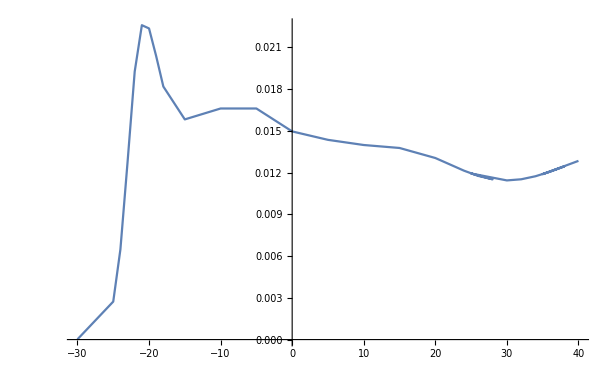

```mathematica
ListPlot[%,Joined->True]
```

```mathematica
ListPointPlot3D[%1685]
```

-Graphics3D-

```mathematica
radiuslistrev=Table[Reverse[radiuslist[[i]]],{i,1,Length[radiuslist]}]
```

{{0.0000182604,-30,1/50},{0.00272832,-25,1/50},{0.00647301,-24,1/50},{0.0127442,-23,1/50},{0.0192545,-22,1/50},{0.0225826,-21,1/50},{0.0223501,-20,1/50},{0.0203572,-19,1/50},{0.0181775,-18,1/50},{0.0158153,-15,1/50},{0.0165989,-10,1/50},{0.0165989,-5,1/50},{0.0149514,0,1/50},{0.014347,5,1/50},{0.0139761,10,1/50},{0.0137627,15,1/50},{0.0130423,20,1/50},{0.0125893,22,1/50},{0.0121339,24,1/50},{0.0117556,26,1/50},{0.0115126,28,1/50},{0.0119309,25,1/50},{0.0114326,30,1/50},{0.0115138,32,1/50},{0.0117327,34,1/50},{0.0120539,36,1/50},{0.0124355,38,1/50},{0.011883,35,1/50},{0.0128367,40,1/50},{3.65821×10^-6,-30,1/100},{0.000609454,-25,1/100},{0.00161416,-24,1/100},{0.00391338,-23,1/100},{0.00794289,-22,1/100},{0.0124277,-21,1/100},{0.0150217,-20,1/100},{0.0152017,-19,1/100},{0.0140624,-18,1/100},{0.0111424,-15,1/100},{0.0120714,-10,1/100},{0.011431,-5,1/100},{0.011315,0,1/100},{0.0110945,5,1/100},{0.0110354,10,1/100},{0.0106603,15,1/100},{0.00968416,20,1/100},{0.00977991,22,1/100},{0.0101051,24,1/100},{0.010937,26,1/100},{0.0119173,28,1/100},{0.0104812,25,1/100},{0.0125355,30,1/100},{0.0120733,32,1/100},{0.0100249,34,1/100},{0.00687354,36,1/100},{0.00391823,38,1/100},{0.00850905,35,1/100},{0.00196966,40,1/100},{1.51974×10^-6,-30,1/150},{0.000260497,-25,1/150},{0.000710489,-24,1/150},{0.00184099,-23,1/150},{0.00423692,-22,1/150},{0.00787119,-21,1/150},{0.0111387,-20,1/150},{0.0124882,-19,1/150},{0.0121451,-18,1/150},{0.00939507,-15,1/150},{0.00999922,-10,1/150},{0.0095923,-5,1/150},{0.00955168,0,1/150},{0.00945794,5,1/150},{0.00944735,10,1/150},{0.00891997,15,1/150},{0.00845268,20,1/150},{0.00897387,22,1/150},{0.00991265,24,1/150},{0.0108352,26,1/150},{0.0108302,28,1/150},{0.0104203,25,1/150},{0.00889094,30,1/150},{0.00544604,32,1/150},{0.00251023,34,1/150},{0.000976367,36,1/150},{0.000354898,38,1/150},{0.00158565,35,1/150},{0.000128235,40,1/150},{8.2838×10^-7,-30,1/200},{0.000143535,-25,1/200},{0.000396719,-24,1/200},{0.00105911,-23,1/200},{0.00259965,-22,1/200},{0.00537605,-21,1/200},{0.00859217,-20,1/200},{0.0105764,-19,1/200},{0.010841,-18,1/200},{0.0084355,-15,1/200},{0.00873323,-10,1/200},{0.00847845,-5,1/200},{0.00845494,0,1/200},{0.00842051,5,1/200},{0.00840535,10,1/200},{0.00782346,15,1/200},{0.00784092,20,1/200},{0.00862111,22,1/200},{0.00958514,24,1/200},{0.00988619,26,1/200},{0.00831149,28,1/200},{0.00989502,25,1/200},{0.00498721,30,1/200},{0.00211987,32,1/200},{0.000735176,34,1/200},{0.000237102,36,1/200},{0.0000760349,38,1/200},{0.000418986,35,1/200},{0.0000254044,40,1/200}}

```mathematica
Table[{radiuslist[[i,2]],radiuslist[[i,3]]},{i,1,29}]
```

{{-30,0.0000182604},{-25,0.00272832},{-24,0.00647301},{-23,0.0127442},{-22,0.0192545},{-21,0.0225826},{-20,0.0223501},{-19,0.0203572},{-18,0.0181775},{-15,0.0158153},{-10,0.0165989},{-5,0.0165989},{0,0.0149514},{5,0.014347},{10,0.0139761},{15,0.0137627},{20,0.0130423},{22,0.0125893},{24,0.0121339},{26,0.0117556},{28,0.0115126},{25,0.0119309},{30,0.0114326},{32,0.0115138},{34,0.0117327},{36,0.0120539},{38,0.0124355},{35,0.011883},{40,0.0128367}}

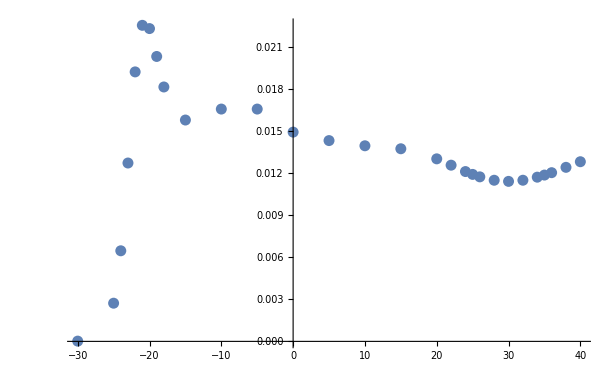

```mathematica
ListPlot[%]
```

```mathematica
Table[{radiuslist[[i,2]],radiuslist[[i,3]]},{i,30,58}]
```

{{-30,3.65821×10^-6},{-25,0.000609454},{-24,0.00161416},{-23,0.00391338},{-22,0.00794289},{-21,0.0124277},{-20,0.0150217},{-19,0.0152017},{-18,0.0140624},{-15,0.0111424},{-10,0.0120714},{-5,0.011431},{0,0.011315},{5,0.0110945},{10,0.0110354},{15,0.0106603},{20,0.00968416},{22,0.00977991},{24,0.0101051},{26,0.010937},{28,0.0119173},{25,0.0104812},{30,0.0125355},{32,0.0120733},{34,0.0100249},{36,0.00687354},{38,0.00391823},{35,0.00850905},{40,0.00196966}}

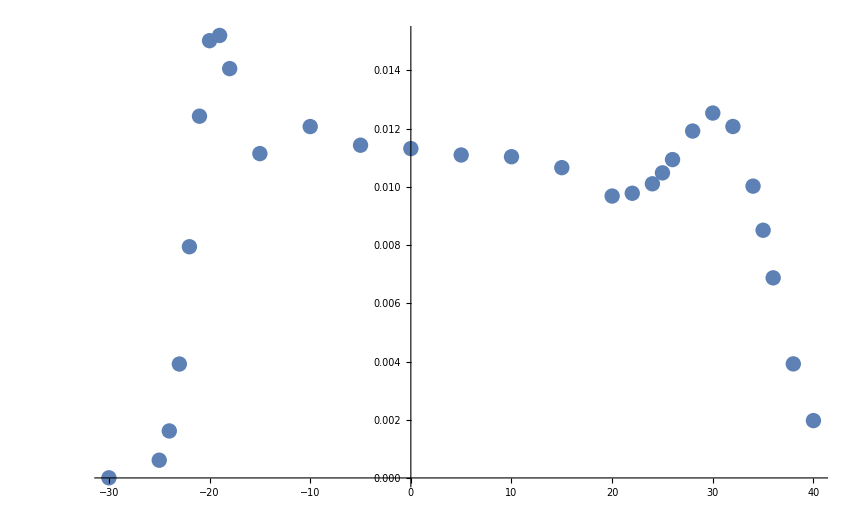

```mathematica
ListPlot[%1319]
```

```mathematica
radiuslistrev2=Table[{radiuslist[[i,2]],radiuslist[[i,1]],radiuslist[[i,3]]},{i,1,Length[radiuslist]}]
```

{{-30,1/50,0.0000182604},{-25,1/50,0.00272832},{-24,1/50,0.00647301},{-23,1/50,0.0127442},{-22,1/50,0.0192545},{-21,1/50,0.0225826},{-20,1/50,0.0223501},{-19,1/50,0.0203572},{-18,1/50,0.0181775},{-15,1/50,0.0158153},{-10,1/50,0.0165989},{-5,1/50,0.0165989},{0,1/50,0.0149514},{5,1/50,0.014347},{10,1/50,0.0139761},{15,1/50,0.0137627},{20,1/50,0.0130423},{22,1/50,0.0125893},{24,1/50,0.0121339},{26,1/50,0.0117556},{28,1/50,0.0115126},{25,1/50,0.0119309},{30,1/50,0.0114326},{32,1/50,0.0115138},{34,1/50,0.0117327},{36,1/50,0.0120539},{38,1/50,0.0124355},{35,1/50,0.011883},{40,1/50,0.0128367},{-30,1/100,3.65821×10^-6},{-25,1/100,0.000609454},{-24,1/100,0.00161416},{-23,1/100,0.00391338},{-22,1/100,0.00794289},{-21,1/100,0.0124277},{-20,1/100,0.0150217},{-19,1/100,0.0152017},{-18,1/100,0.0140624},{-15,1/100,0.0111424},{-10,1/100,0.0120714},{-5,1/100,0.011431},{0,1/100,0.011315},{5,1/100,0.0110945},{10,1/100,0.0110354},{15,1/100,0.0106603},{20,1/100,0.00968416},{22,1/100,0.00977991},{24,1/100,0.0101051},{26,1/100,0.010937},{28,1/100,0.0119173},{25,1/100,0.0104812},{30,1/100,0.0125355},{32,1/100,0.0120733},{34,1/100,0.0100249},{36,1/100,0.00687354},{38,1/100,0.00391823},{35,1/100,0.00850905},{40,1/100,0.00196966},{-30,1/150,1.51974×10^-6},{-25,1/150,0.000260497},{-24,1/150,0.000710489},{-23,1/150,0.00184099},{-22,1/150,0.00423692},{-21,1/150,0.00787119},{-20,1/150,0.0111387},{-19,1/150,0.0124882},{-18,1/150,0.0121451},{-15,1/150,0.00939507},{-10,1/150,0.00999922},{-5,1/150,0.0095923},{0,1/150,0.00955168},{5,1/150,0.00945794},{10,1/150,0.00944735},{15,1/150,0.00891997},{20,1/150,0.00845268},{22,1/150,0.00897387},{24,1/150,0.00991265},{26,1/150,0.0108352},{28,1/150,0.0108302},{25,1/150,0.0104203},{30,1/150,0.00889094},{32,1/150,0.00544604},{34,1/150,0.00251023},{36,1/150,0.000976367},{38,1/150,0.000354898},{35,1/150,0.00158565},{40,1/150,0.000128235},{-30,1/200,8.2838×10^-7},{-25,1/200,0.000143535},{-24,1/200,0.000396719},{-23,1/200,0.00105911},{-22,1/200,0.00259965},{-21,1/200,0.00537605},{-20,1/200,0.00859217},{-19,1/200,0.0105764},{-18,1/200,0.010841},{-15,1/200,0.0084355},{-10,1/200,0.00873323},{-5,1/200,0.00847845},{0,1/200,0.00845494},{5,1/200,0.00842051},{10,1/200,0.00840535},{15,1/200,0.00782346},{20,1/200,0.00784092},{22,1/200,0.00862111},{24,1/200,0.00958514},{26,1/200,0.00988619},{28,1/200,0.00831149},{25,1/200,0.00989502},{30,1/200,0.00498721},{32,1/200,0.00211987},{34,1/200,0.000735176},{36,1/200,0.000237102},{38,1/200,0.0000760349},{35,1/200,0.000418986},{40,1/200,0.0000254044}}

```mathematica
radiuslistrev3=Table[{radiuslist[[i,2]],radiuslist[[i,1]],1/radiuslist[[i,3]]},{i,1,Length[radiuslist]}]
```

{{-30,1/50,54763.3},{-25,1/50,366.525},{-24,1/50,154.488},{-23,1/50,78.4671},{-22,1/50,51.936},{-21,1/50,44.282},{-20,1/50,44.7426},{-19,1/50,49.1228},{-18,1/50,55.0129},{-15,1/50,63.2298},{-10,1/50,60.245},{-5,1/50,60.245},{0,1/50,66.8836},{5,1/50,69.7009},{10,1/50,71.5507},{15,1/50,72.66},{20,1/50,76.6735},{22,1/50,79.4328},{24,1/50,82.4138},{26,1/50,85.0658},{28,1/50,86.861},{25,1/50,83.8158},{30,1/50,87.4688},{32,1/50,86.8525},{34,1/50,85.232},{36,1/50,82.9609},{38,1/50,80.4148},{35,1/50,84.1535},{40,1/50,77.9018},{-30,1/100,273358.},{-25,1/100,1640.81},{-24,1/100,619.519},{-23,1/100,255.533},{-22,1/100,125.899},{-21,1/100,80.4657},{-20,1/100,66.5704},{-19,1/100,65.7823},{-18,1/100,71.1114},{-15,1/100,89.7477},{-10,1/100,82.8406},{-5,1/100,87.4813},{0,1/100,88.3785},{5,1/100,90.135},{10,1/100,90.6175},{15,1/100,93.8063},{20,1/100,103.261},{22,1/100,102.25},{24,1/100,98.9599},{26,1/100,91.4332},{28,1/100,83.9115},{25,1/100,95.4093},{30,1/100,79.7733},{32,1/100,82.8276},{34,1/100,99.7517},{36,1/100,145.485},{38,1/100,255.217},{35,1/100,117.522},{40,1/100,507.702},{-30,1/150,658009.},{-25,1/150,3838.82},{-24,1/150,1407.48},{-23,1/150,543.186},{-22,1/150,236.021},{-21,1/150,127.046},{-20,1/150,89.7775},{-19,1/150,80.0755},{-18,1/150,82.3379},{-15,1/150,106.439},{-10,1/150,100.008},{-5,1/150,104.25},{0,1/150,104.694},{5,1/150,105.731},{10,1/150,105.85},{15,1/150,112.108},{20,1/150,118.306},{22,1/150,111.435},{24,1/150,100.881},{26,1/150,92.2922},{28,1/150,92.334},{25,1/150,95.9663},{30,1/150,112.474},{32,1/150,183.62},{34,1/150,398.37},{36,1/150,1024.21},{38,1/150,2817.71},{35,1/150,630.657},{40,1/150,7798.17},{-30,1/200,1.20717×10^6},{-25,1/200,6966.95},{-24,1/200,2520.68},{-23,1/200,944.193},{-22,1/200,384.667},{-21,1/200,186.01},{-20,1/200,116.385},{-19,1/200,94.55},{-18,1/200,92.2421},{-15,1/200,118.547},{-10,1/200,114.505},{-5,1/200,117.946},{0,1/200,118.274},{5,1/200,118.758},{10,1/200,118.972},{15,1/200,127.821},{20,1/200,127.536},{22,1/200,115.994},{24,1/200,104.328},{26,1/200,101.151},{28,1/200,120.315},{25,1/200,101.061},{30,1/200,200.513},{32,1/200,471.728},{34,1/200,1360.22},{36,1/200,4217.59},{38,1/200,13151.9},{35,1/200,2386.71},{40,1/200,39363.2}}

```mathematica
radiuslistrev3b=Table[{radiuslist[[i,1]],1/radiuslist[[i,3]]},{i,1,Length[radiuslist]}]
```

{{1/50,54763.3},{1/50,366.525},{1/50,154.488},{1/50,78.4671},{1/50,51.936},{1/50,44.282},{1/50,44.7426},{1/50,49.1228},{1/50,55.0129},{1/50,63.2298},{1/50,60.245},{1/50,60.245},{1/50,66.8836},{1/50,69.7009},{1/50,71.5507},{1/50,72.66},{1/50,76.6735},{1/50,79.4328},{1/50,82.4138},{1/50,85.0658},{1/50,86.861},{1/50,83.8158},{1/50,87.4688},{1/50,86.8525},{1/50,85.232},{1/50,82.9609},{1/50,80.4148},{1/50,84.1535},{1/50,77.9018},{1/100,273358.},{1/100,1640.81},{1/100,619.519},{1/100,255.533},{1/100,125.899},{1/100,80.4657},{1/100,66.5704},{1/100,65.7823},{1/100,71.1114},{1/100,89.7477},{1/100,82.8406},{1/100,87.4813},{1/100,88.3785},{1/100,90.135},{1/100,90.6175},{1/100,93.8063},{1/100,103.261},{1/100,102.25},{1/100,98.9599},{1/100,91.4332},{1/100,83.9115},{1/100,95.4093},{1/100,79.7733},{1/100,82.8276},{1/100,99.7517},{1/100,145.485},{1/100,255.217},{1/100,117.522},{1/100,507.702},{1/150,658009.},{1/150,3838.82},{1/150,1407.48},{1/150,543.186},{1/150,236.021},{1/150,127.046},{1/150,89.7775},{1/150,80.0755},{1/150,82.3379},{1/150,106.439},{1/150,100.008},{1/150,104.25},{1/150,104.694},{1/150,105.731},{1/150,105.85},{1/150,112.108},{1/150,118.306},{1/150,111.435},{1/150,100.881},{1/150,92.2922},{1/150,92.334},{1/150,95.9663},{1/150,112.474},{1/150,183.62},{1/150,398.37},{1/150,1024.21},{1/150,2817.71},{1/150,630.657},{1/150,7798.17},{1/200,1.20717×10^6},{1/200,6966.95},{1/200,2520.68},{1/200,944.193},{1/200,384.667},{1/200,186.01},{1/200,116.385},{1/200,94.55},{1/200,92.2421},{1/200,118.547},{1/200,114.505},{1/200,117.946},{1/200,118.274},{1/200,118.758},{1/200,118.972},{1/200,127.821},{1/200,127.536},{1/200,115.994},{1/200,104.328},{1/200,101.151},{1/200,120.315},{1/200,101.061},{1/200,200.513},{1/200,471.728},{1/200,1360.22},{1/200,4217.59},{1/200,13151.9},{1/200,2386.71},{1/200,39363.2}}

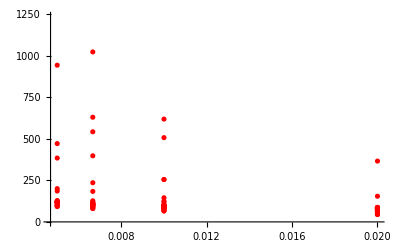

```mathematica
ListPlot[radiuslistrev3b,PlotStyle->Red]
```

```mathematica
Table[{radiuslist[[i,1]],1/radiuslist[[i,3]]},{i,59,87}]
```

{{1/150,658009.},{1/150,3838.82},{1/150,1407.48},{1/150,543.186},{1/150,236.021},{1/150,127.046},{1/150,89.7775},{1/150,80.0755},{1/150,82.3379},{1/150,106.439},{1/150,100.008},{1/150,104.25},{1/150,104.694},{1/150,105.731},{1/150,105.85},{1/150,112.108},{1/150,118.306},{1/150,111.435},{1/150,100.881},{1/150,92.2922},{1/150,92.334},{1/150,95.9663},{1/150,112.474},{1/150,183.62},{1/150,398.37},{1/150,1024.21},{1/150,2817.71},{1/150,630.657},{1/150,7798.17}}

```mathematica
radiustempb={{0.000018260411506109625,0.014141591331702053},{0.0027283240761857295,0.01406660183151031},{0.006473013249120428,0.013957442390134713},{0.01274419145456678,0.013743434583025528},{0.019254458773335127,0.013426200078767481},{0.02258255083760387,0.013077962319696074},{0.022350052047681666,0.01276908621262373},{0.02035716522515999,0.012518124389331184},{0.01817754275253453,0.012311805310455939},{0.015815331642024293,0.01178065439762513},{0.016598899560664637,0.010879360214414616},{0.016598899560664637,0.010122806356092126},{0.014951353127558388,0.009457452432140618},{0.01434702065586793,0.0088744978189348},{0.01397609750473885,0.008357640344532877},{0.013762725385578588,0.007900222283576347},{0.013042321891923997,0.007494427075601331},{0.012589253275232566,0.0073426698124556605},{0.012133896395914901,0.007195405109857138},{0.01175560188099104,0.007052199268395599},{0.01151264060041704,0.00691305683736121},{0.011930918682798358,0.007123303013356376},{0.01143264708112282,0.006778251453630603},{0.01151377132532228,0.006648137186286674},{0.01173268058212253,0.006523011621084433},{0.01205386937172231,0.00640304082683379},{0.012435528395274788,0.006288246078935864},{0.011883043701945093,0.006462376860922777},{0.012836672529596152,0.0061785215098166014},{3.6582095867433203*^-6,0.007071019178143946},{0.0006094542059485861,0.007064000557520464},{0.0016141558363718046,0.007052603378591086},{0.0039133834514276464,0.007025537112975037},{0.007942891718182467,0.0069712639759529965},{0.012427662341874183,0.006888165068327471},{0.015021700089362657,0.006793857219330731},{0.015201661319220298,0.006707889004366455},{0.014062438111768629,0.006636566662265026},{0.011142352972522468,0.006472524444318641},{0.012071372744993635,0.006195023433990477},{0.011431013741690386,0.005938136072851764},{0.011314971368916403,0.005701424402948094},{0.011094471800664384,0.00548239108566746},{0.011035391509840788,0.005279884040544779},{0.010660262231890382,0.0050946781035422},{0.009684157347847826,0.00491843895407569},{0.009779914544215538,0.004848117896033559},{0.010105099993926473,0.004778988847274816},{0.010936951683979191,0.004712862856025578},{0.011917319754972537,0.004651714019880762},{0.010481156189247175,0.004745424224548714},{0.01253552093727533,0.0045969833946620945},{0.0120732660218269,0.004548421034816461},{0.010024888431061184,0.004502597321201563},{0.006873537919106621,0.004453419322055297},{0.003918226862816113,0.004396684265454686},{0.00850904566330982,0.004478800877836945},{0.0019696582538042246,0.004333298666936786},{1.5197354659926742*^-6,0.0047140334105477836},{0.0002604968159390144,0.004712305780146753},{0.0007104888625758621,0.004709418511053818},{0.0018409883245819234,0.004702148924797023},{0.0042369185526497655,0.004685741062547548},{0.007871190093845667,0.004655673739372068},{0.011138651753354534,0.004614569008958014},{0.012488207265595184,0.00457206041743788},{0.012145077617196146,0.004535011671065287},{0.009395069976148616,0.004453475239884342},{0.009999217905772104,0.004322433350817311},{0.009592299841600246,0.004194582290094954},{0.009551683432987217,0.004074888915271146},{0.00945794498243872,0.003961356352973415},{0.00944735369675308,0.0038545381035832646},{0.00891997164323387,0.0037547546897472067},{0.008452683741929435,0.0036552604066663833},{0.008973869235055597,0.0036154592094185963},{0.009912653262392846,0.0035776564786199096},{0.010835152742052403,0.0035437419872227315},{0.010830246443564569,0.003514796975953238},{0.010420329671405418,0.003560106585383398},{0.008890940587472064,0.003488820138983363},{0.00544604305732901,0.0034596238050477166},{0.0025102289211547083,0.0034225740050556376},{0.0009763666816033828,0.0033794442948731416},{0.00035489841864708534,0.0033340597113230472},{0.0015856485432869246,0.0034015074412049994},{0.00012823525429996589,0.003288717677778273},{8.283804106398101*^-7,0.003535529591290214},{0.0001435348899202893,0.0035348921317192184},{0.00039671895768747685,0.0035338137116315634},{0.001059105486389808,0.00353103262466543},{0.002599648463080759,0.0035243715054763354},{0.005376045144575103,0.003510807713893698},{0.00859217495830709,0.0034895869904856954},{0.010576411949451147,0.003464973335826146},{0.010841040951994578,0.0034421756352771143},{0.008435503123218018,0.003392481360588298},{0.00873323181168797,0.0033168937898592},{0.008478449506119775,0.0032405915902511623},{0.00845493968317887,0.0031686574433667076},{0.008420507601551228,0.003099454186964796},{0.008405351649942753,0.0030337231500136607},{0.007823462594103511,0.0029712950447339757},{0.007840922509865284,0.0029074803946637223},{0.00862111263757731,0.0028824586717901236},{0.009585140951529831,0.002859650169443721},{0.009886188733378145,0.002840316878649514},{0.00831148555751278,0.0028236888303338065},{0.009895018802377373,0.002849518761588638},{0.0049872081804839714,0.0028051158614542425},{0.0021198655061727945,0.002780299736808111},{0.0007351761008472254,0.0027505629985907203},{0.00023710240993525514,0.002719036904761638},{0.00007603488841246695,0.0026874512709258802},{0.000418986146093657,0.0027348789218316276},{0.000025404409453196218,0.0026564219424725023}};
```

```mathematica
invradiustempb={{54763.27845434463,0.014141591331702053},{366.52537311404257,0.01406660183151031},{154.48755649247016,0.013957442390134713},{78.46711998678096,0.013743434583025528},{51.936022288243564,0.013426200078767481},{44.281977142051915,0.013077962319696074},{44.7426251118609,0.01276908621262373},{49.122753042455635,0.012518124389331184},{55.012936215516156,0.012311805310455939},{63.229783771515294,0.01178065439762513},{60.2449575856075,0.010879360214414616},{60.2449575856075,0.010122806356092126},{66.88357846065426,0.009457452432140618},{69.70088243310643,0.0088744978189348},{71.5507315014747,0.008357640344532877},{72.66002713734738,0.007900222283576347},{76.67346414898832,0.007494427075601331},{79.4328287895635,0.0073426698124556605},{82.41375790357567,0.007195405109857138},{85.06582734968364,0.007052199268395599},{86.86104558529999,0.00691305683736121},{83.81584239961086,0.007123303013356376},{87.46880690922092,0.006778251453630603},{86.85251528321535,0.006648137186286674},{85.23201437220858,0.006523011621084433},{82.9609123146749,0.00640304082683379},{80.41475747664866,0.006288246078935864},{84.15352371684988,0.006462376860922777},{77.90180809663924,0.0061785215098166014},{273357.76594753243,0.007071019178143946},{1640.812369886837,0.007064000557520464},{619.5188701530426,0.007052603378591086},{255.53335429861562,0.007025537112975037},{125.89873253727612,0.0069712639759529965},{80.4656557678242,0.006888165068327471},{66.57036114761283,0.006793857219330731},{65.78228385707061,0.006707889004366455},{71.11142406828557,0.006636566662265026},{89.74765047077973,0.006472524444318641},{82.8406197973408,0.006195023433990477},{87.48130503534175,0.005938136072851764},{88.37848257814608,0.005701424402948094},{90.13498055311798,0.00548239108566746},{90.61753714023213,0.005279884040544779},{93.80632279461949,0.0050946781035422},{103.26143660008132,0.00491843895407569},{102.25038219699613,0.004848117896033559},{98.9599311833664,0.004778988847274816},{91.43315513268959,0.004712862856025578},{83.91148517960568,0.004651714019880762},{95.40932144737235,0.004745424224548714},{79.77331018022741,0.0045969833946620945},{82.82762909324863,0.004548421034816461},{99.75173358554227,0.004502597321201563},{145.48548531612286,0.004453419322055297},{255.21748357400588,0.004396684265454686},{117.52199242647187,0.004478800877836945},{507.702286967085,0.004333298666936786},{658009.253832088,0.0047140334105477836},{3838.8185145192433,0.004712305780146753},{1407.4815984792801,0.004709418511053818},{543.1864975173559,0.004702148924797023},{236.0205860871696,0.004685741062547548},{127.04559133718303,0.004655673739372068},{89.77747236768026,0.004614569008958014},{80.075544770544,0.00457206041743788},{82.33788465741098,0.004535011671065287},{106.43880274853862,0.004453475239884342},{100.00782155399818,0.004322433350817311},{104.25028580353195,0.004194582290094954},{104.69358694891937,0.004074888915271146},{105.73121347785121,0.003961356352973415},{105.84974714598499,0.0038545381035832646},{112.10797971073565,0.0037547546897472067},{118.30562109398606,0.0036552604066663833},{111.43465252352817,0.0036154592094185963},{100.88116405663592,0.0035776564786199096},{92.29219225668056,0.0035437419872227315},{92.33400229726159,0.003514796975953238},{95.96625361519175,0.003560106585383398},{112.47403918198121,0.003488820138983363},{183.6195545046693,0.0034596238050477166},{398.37004170121617,0.0034225740050556376},{1024.205371651772,0.0033794442948731416},{2817.707680445909,0.0033340597113230472},{630.6567771487865,0.0034015074412049994},{7798.167558983552,0.003288717677778273},{1.2071748524661965*^6,0.003535529591290214},{6966.947203953967,0.0035348921317192184},{2520.6761124528102,0.0035338137116315634},{944.1930127363593,0.00353103262466543},{384.6673941502585,0.0035243715054763354},{186.01034275336897,0.003510807713893698},{116.38496711861991,0.0034895869904856954},{94.55002365446762,0.003464973335826146},{92.24206461613042,0.0034421756352771143},{118.54657456620264,0.003392481360588298},{114.50514787225359,0.0033168937898592},{117.94609371420994,0.0032405915902511623},{118.27405486871815,0.0031686574433667076},{118.75768627247362,0.003099454186964796},{118.97182195902664,0.0030337231500136607},{127.82064053756619,0.0029712950447339757},{127.5360136185278,0.0029074803946637223},{115.99430862801233,0.0028824586717901236},{104.32814760438087,0.002859650169443721},{101.15121478753082,0.002840316878649514},{120.315434958086,0.0028236888303338065},{101.06094995592534,0.002849518761588638},{200.51298518341727,0.0028051158614542425},{471.7280398629629,0.002780299736808111},{1360.2183189137793,0.0027505629985907203},{4217.5868236559345,0.002719036904761638},{13151.85727077409,0.0026874512709258802},{2386.7137596870984,0.0027348789218316276},{39363.245260329655,0.0026564219424725023}};
```

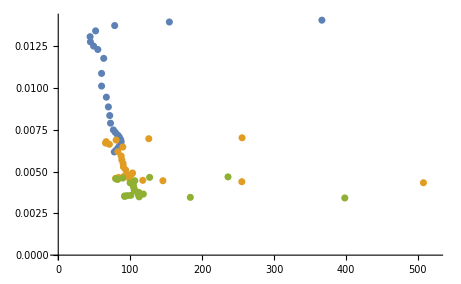

```mathematica
ListPlot[{Table[invradiustempb[[i]],{i,1,29}],Table[invradiustempb[[i]],{i,30,58}],Table[invradiustempb[[i]],{i,59,87}]}]
```

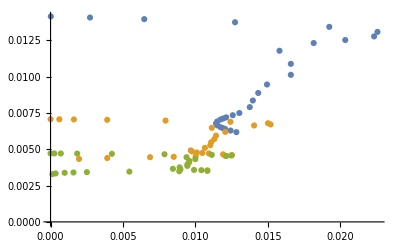

```mathematica
ListPlot[{Table[radiustempb[[i]],{i,1,29}],Table[radiustempb[[i]],{i,30,58}],Table[radiustempb[[i]],{i,59,87}]}]
```

```mathematica
radiuslistrev3c=Table[{radiuslist[[i,2]],1/radiuslist[[i,3]]},{i,1,Length[radiuslist]}]
```

{{-30,54763.3},{-25,366.525},{-24,154.488},{-23,78.4671},{-22,51.936},{-21,44.282},{-20,44.7426},{-19,49.1228},{-18,55.0129},{-15,63.2298},{-10,60.245},{-5,60.245},{0,66.8836},{5,69.7009},{10,71.5507},{15,72.66},{20,76.6735},{22,79.4328},{24,82.4138},{26,85.0658},{28,86.861},{25,83.8158},{30,87.4688},{32,86.8525},{34,85.232},{36,82.9609},{38,80.4148},{35,84.1535},{40,77.9018},{-30,273358.},{-25,1640.81},{-24,619.519},{-23,255.533},{-22,125.899},{-21,80.4657},{-20,66.5704},{-19,65.7823},{-18,71.1114},{-15,89.7477},{-10,82.8406},{-5,87.4813},{0,88.3785},{5,90.135},{10,90.6175},{15,93.8063},{20,103.261},{22,102.25},{24,98.9599},{26,91.4332},{28,83.9115},{25,95.4093},{30,79.7733},{32,82.8276},{34,99.7517},{36,145.485},{38,255.217},{35,117.522},{40,507.702},{-30,658009.},{-25,3838.82},{-24,1407.48},{-23,543.186},{-22,236.021},{-21,127.046},{-20,89.7775},{-19,80.0755},{-18,82.3379},{-15,106.439},{-10,100.008},{-5,104.25},{0,104.694},{5,105.731},{10,105.85},{15,112.108},{20,118.306},{22,111.435},{24,100.881},{26,92.2922},{28,92.334},{25,95.9663},{30,112.474},{32,183.62},{34,398.37},{36,1024.21},{38,2817.71},{35,630.657},{40,7798.17},{-30,1.20717×10^6},{-25,6966.95},{-24,2520.68},{-23,944.193},{-22,384.667},{-21,186.01},{-20,116.385},{-19,94.55},{-18,92.2421},{-15,118.547},{-10,114.505},{-5,117.946},{0,118.274},{5,118.758},{10,118.972},{15,127.821},{20,127.536},{22,115.994},{24,104.328},{26,101.151},{28,120.315},{25,101.061},{30,200.513},{32,471.728},{34,1360.22},{36,4217.59},{38,13151.9},{35,2386.71},{40,39363.2}}

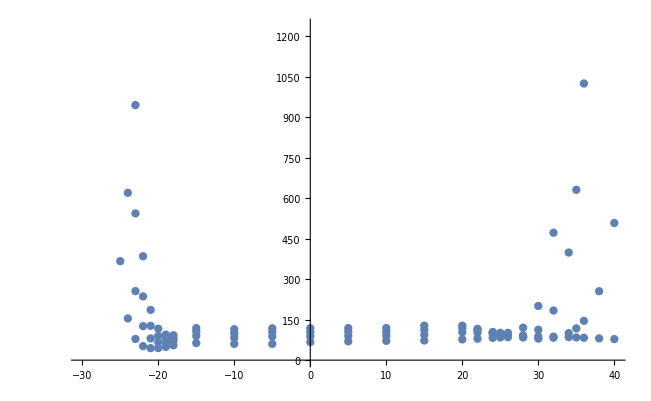

```mathematica
ListPlot[radiuslistrev3c]
```

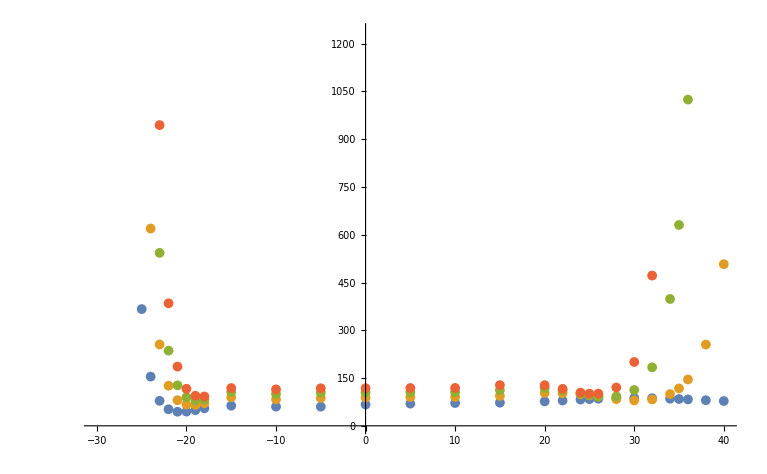

```mathematica
ListPlot[{Table[radiuslistrev3c[[i]],{i,1,29}],Table[radiuslistrev3c[[i]],{i,30,58}],Table[radiuslistrev3c[[i]],{i,59,87}],Table[radiuslistrev3c[[i]],{i,88,116}]}]
```

Temp 1/50

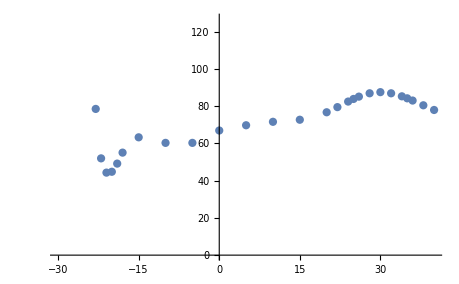

```mathematica
ListPlot[{Table[radiuslistrev3c[[i]],{i,1,29}]}]
```

Temp 1/100

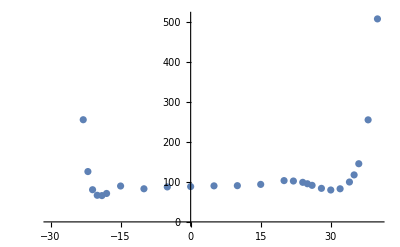

```mathematica
ListPlot[{Table[radiuslistrev3c[[i]],{i,30,58}]}]
```

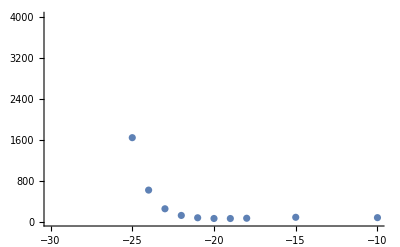

```mathematica
ListPlot[{Table[radiuslistrev3c[[i]],{i,30,40}]}]
```

```mathematica
Sort@Table[radiuslistrev3c[[i]],{i,31,37}]
```

{{-25,1640.81},{-24,619.519},{-23,255.533},{-22,125.899},{-21,80.4657},{-20,66.5704},{-19,65.7823}}

```mathematica
nlm=NonlinearModelFit[Table[radiuslistrev3c[[i]],{i,31,36}],{a*(x-t1)^3+b},{a,b,t1},x]
```

FittedModel[106.759-31.4276 (21.3651+x)^3]

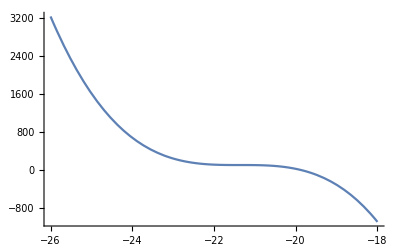

```mathematica
Plot[nlm[x],{x,-26,-18}]
```

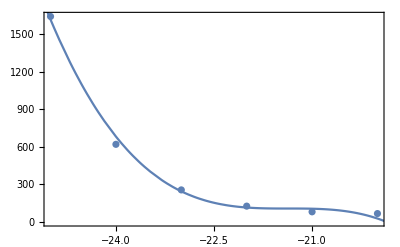

```mathematica
Show[ListPlot[Table[radiuslistrev3c[[i]],{i,31,36}]],Plot[nlm[x],{x,-26,40}],Frame->True]
```

```mathematica
FittedModel
```

Temp 1/150

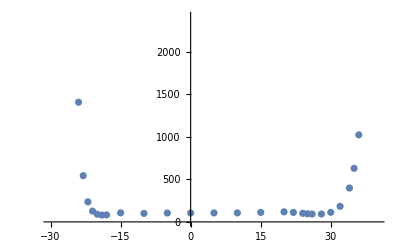

```mathematica
ListPlot[{Table[radiuslistrev3c[[i]],{i,59,87}]}]
```

Temp 1/200

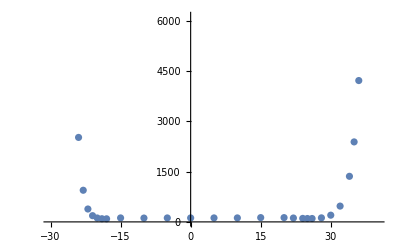

```mathematica
ListPlot[{Table[radiuslistrev3c[[i]],{i,88,116}]}]
```

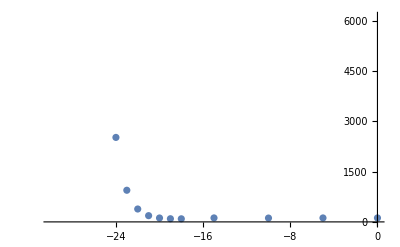

```mathematica
ListPlot[{Table[radiuslistrev3c[[i]],{i,88,100}]}]
```

## Masa vs Radius

```mathematica
radiuslist[[1,3]]
```

0.0000182604

```mathematica
Table[{radiuslist[[i,3]],fmasab[radiuslist[[i,2]],radiuslist[[i,1]]]},{i,1,Length[radiuslist]}]
```

```mathematica
masavsradio={{0.000018260411506109625,7.67012542656056*^-6},{0.0027283240761857295,0.0010271468819041299},{0.006473013249120428,0.00238619496510356},{0.01274419145456678,0.004625167743095372},{0.019254458773335127,0.006925307586308346},{0.02258255083760387,0.00806910734938551},{0.022350052047681666,0.007921239835511492},{0.02035716522515999,0.007134822797452347},{0.01817754275253453,0.006285035258687384},{0.015815331642024293,0.005232971632653512},{0.016598899560664637,0.00517226706383063},{0.016598899560664637,0.004533278399429165},{0.014951353127558388,0.004146287409150788},{0.01434702065586793,0.0037683602047091196},{0.01397609750473885,0.0034858575192352717},{0.013762725385578588,0.003264008883252036},{0.013042321891923997,0.002942286664888617},{0.012589253275232566,0.0027857903871961586},{0.012133896395914901,0.0026359341881309305},{0.01175560188099104,0.002509350336332165},{0.01151264060041704,0.002417026439245529},{0.011930918682798358,0.0025688833931137166},{0.01143264708112282,0.0023625256326832798},{0.01151377132532228,0.002343167479430964},{0.01173268058212253,0.0023520994561256436},{0.01205386937172231,0.002380496549371348},{0.012435528395274788,0.0024190539290088247},{0.011883043701945093,0.002364471879113616},{0.012836672529596152,0.0024587968875757473},{3.6582095867433203*^-6,9.326240913013963*^-7},{0.0006094542059485861,0.00013372069114029852},{0.0016141558363718046,0.0003435087137641976},{0.0039133834514276464,0.0008123183106069603},{0.007942891718182467,0.0016266995623419845},{0.012427662341874183,0.0025429947154077437},{0.015021700089362657,0.003086998598509983},{0.015201661319220298,0.0031270703990408906},{0.014062438111768629,0.002878614303407921},{0.011142352972522468,0.0022060671747795445},{0.012071372744993635,0.002291719943699947},{0.011431013741690386,0.0020853497111944204},{0.011314971368916403,0.001986719168724856},{0.011094471800664384,0.001877707638999087},{0.011035391509840788,0.0018020083780121892},{0.010660262231890382,0.0016770185597786362},{0.009684157347847826,0.0014735726750687086},{0.009779914544215538,0.0014572111193452814},{0.010105099993926473,0.0015092065941211355},{0.010936951683979191,0.0016181772028671874},{0.011917319754972537,0.0017409905188196224},{0.010481156189247175,0.0015584229098954253},{0.01253552093727533,0.0017989590790275735},{0.0120732660218269,0.0016920367128715683},{0.010024888431061184,0.0013683930323140957},{0.006873537919106621,0.000917670254128734},{0.003918226862816113,0.0005176042856101862},{0.00850904566330982,0.0011477126474544466},{0.0019696582538042246,0.000260269752652913},{1.5197354659926742*^-6,2.734076985460834*^-7},{0.0002604968159390144,0.000039849747698036255},{0.0007104888625758621,0.00010511225405006466},{0.0018409883245819234,0.0002641334352456822},{0.0042369185526497655,0.0005951657757818768},{0.007871190093845667,0.001099510775080021},{0.011138651753354534,0.0015670387527511494},{0.012488207265595184,0.0017722202920043154},{0.012145077617196146,0.0017279320989131886},{0.009395069976148616,0.0013060084132312962},{0.009999217905772104,0.0013428520506124026},{0.009592299841600246,0.0012521633445273996},{0.009551683432987217,0.0012115955475835443},{0.00945794498243872,0.0011674090294467073},{0.00944735369675308,0.001134437044931115},{0.00891997164323387,0.0010398986096883875},{0.008452683741929435,0.000965613202400816},{0.008973869235055597,0.0010201466175955689},{0.009912653262392846,0.0011191298997884707},{0.010835152742052403,0.0012077628165525723},{0.010830246443564569,0.0011810657930550472},{0.010420329671405418,0.0011702127719122567},{0.008890940587472064,0.0009423374649622617},{0.00544604305732901,0.0005651026798990517},{0.0025102289211547083,0.00026007975047151336},{0.0009763666816033828,0.00010249231268117062},{0.00035489841864708534,0.00003809197057700383},{0.0015856485432869246,0.00016526867276328984},{0.00012823525429996589,0.00001404270827191479},{8.283804106398101*^-7,1.1471327514743074*^-7},{0.0001435348899202893,0.0000168487560991162},{0.00039671895768747685,0.0000449095313090804},{0.001059105486389808,0.00011588026868143452},{0.002599648463080759,0.0002770080864475841},{0.005376045144575103,0.0005660829536314011},{0.00859217495830709,0.0009090279805190756},{0.010576411949451147,0.0011329041645962554},{0.010841040951994578,0.001170697376287915},{0.008435503123218018,0.0008980872653440796},{0.00873323181168797,0.0009012068759349856},{0.008478449506119775,0.0008565379500921285},{0.00845493968317887,0.0008346667563453293},{0.008420507601551228,0.000813509412230392},{0.008405351649942753,0.0007938755151244693},{0.007823462594103511,0.0007212988255118247},{0.007840922509865284,0.0007145849264684721},{0.00862111263757731,0.0007830982878988298},{0.009585140951529831,0.0008629063164709077},{0.009886188733378145,0.0008730647181243161},{0.00831148555751278,0.0007136966381802194},{0.009895018802377373,0.0008836295898466879},{0.0049872081804839714,0.0004185437805593911},{0.0021198655061727945,0.00017815705308085996},{0.0007351761008472254,0.00006311283848502677},{0.00023710240993525514,0.000020984481156220767},{0.00007603488841246695,6.921500561561144*^-6},{0.000418986146093657,0.00003649365411975319},{0.000025404409453196218,2.375868595696599*^-6}};
```

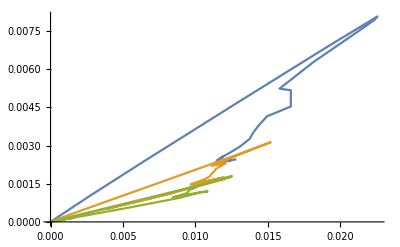

```mathematica
ListPlot[{Table[masavsradio[[i]],{i,1,29}],Table[masavsradio[[i]],{i,30,58}],Table[masavsradio[[i]],{i,59,87}]},Joined->True]
```

```mathematica
radiuslistrev=Table[Reverse[radiuslist[[i]]],{i,1,Length[radiuslist]}]
```

{{0.0000182604,-30,1/50},{0.00272832,-25,1/50},{0.00647301,-24,1/50},{0.0127442,-23,1/50},{0.0192545,-22,1/50},{0.0225826,-21,1/50},{0.0223501,-20,1/50},{0.0203572,-19,1/50},{0.0181775,-18,1/50},{0.0158153,-15,1/50},{0.0165989,-10,1/50},{0.0165989,-5,1/50},{0.0149514,0,1/50},{0.014347,5,1/50},{0.0139761,10,1/50},{0.0137627,15,1/50},{0.0130423,20,1/50},{0.0125893,22,1/50},{0.0121339,24,1/50},{0.0117556,26,1/50},{0.0115126,28,1/50},{0.0119309,25,1/50},{0.0114326,30,1/50},{0.0115138,32,1/50},{0.0117327,34,1/50},{0.0120539,36,1/50},{0.0124355,38,1/50},{0.011883,35,1/50},{0.0128367,40,1/50},{3.65821×10^-6,-30,1/100},{0.000609454,-25,1/100},{0.00161416,-24,1/100},{0.00391338,-23,1/100},{0.00794289,-22,1/100},{0.0124277,-21,1/100},{0.0150217,-20,1/100},{0.0152017,-19,1/100},{0.0140624,-18,1/100},{0.0111424,-15,1/100},{0.0120714,-10,1/100},{0.011431,-5,1/100},{0.011315,0,1/100},{0.0110945,5,1/100},{0.0110354,10,1/100},{0.0106603,15,1/100},{0.00968416,20,1/100},{0.00977991,22,1/100},{0.0101051,24,1/100},{0.010937,26,1/100},{0.0119173,28,1/100},{0.0104812,25,1/100},{0.0125355,30,1/100},{0.0120733,32,1/100},{0.0100249,34,1/100},{0.00687354,36,1/100},{0.00391823,38,1/100},{0.00850905,35,1/100},{0.00196966,40,1/100},{1.51974×10^-6,-30,1/150},{0.000260497,-25,1/150},{0.000710489,-24,1/150},{0.00184099,-23,1/150},{0.00423692,-22,1/150},{0.00787119,-21,1/150},{0.0111387,-20,1/150},{0.0124882,-19,1/150},{0.0121451,-18,1/150},{0.00939507,-15,1/150},{0.00999922,-10,1/150},{0.0095923,-5,1/150},{0.00955168,0,1/150},{0.00945794,5,1/150},{0.00944735,10,1/150},{0.00891997,15,1/150},{0.00845268,20,1/150},{0.00897387,22,1/150},{0.00991265,24,1/150},{0.0108352,26,1/150},{0.0108302,28,1/150},{0.0104203,25,1/150},{0.00889094,30,1/150},{0.00544604,32,1/150},{0.00251023,34,1/150},{0.000976367,36,1/150},{0.000354898,38,1/150},{0.00158565,35,1/150},{0.000128235,40,1/150},{8.2838×10^-7,-30,1/200},{0.000143535,-25,1/200},{0.000396719,-24,1/200},{0.00105911,-23,1/200},{0.00259965,-22,1/200},{0.00537605,-21,1/200},{0.00859217,-20,1/200},{0.0105764,-19,1/200},{0.010841,-18,1/200},{0.0084355,-15,1/200},{0.00873323,-10,1/200},{0.00847845,-5,1/200},{0.00845494,0,1/200},{0.00842051,5,1/200},{0.00840535,10,1/200},{0.00782346,15,1/200},{0.00784092,20,1/200},{0.00862111,22,1/200},{0.00958514,24,1/200},{0.00988619,26,1/200},{0.00831149,28,1/200},{0.00989502,25,1/200},{0.00498721,30,1/200},{0.00211987,32,1/200},{0.000735176,34,1/200},{0.000237102,36,1/200},{0.0000760349,38,1/200},{0.000418986,35,1/200},{0.0000254044,40,1/200}}

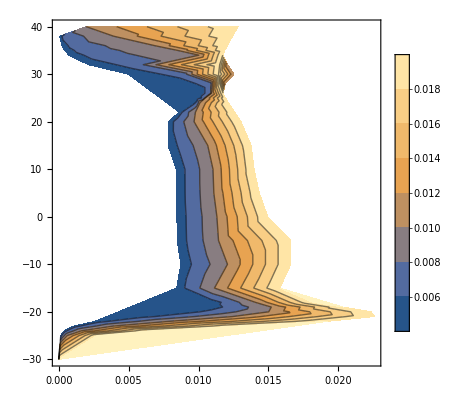

```mathematica
ListContourPlot[radiuslistrev,PlotLegends->Automatic,PlotRange->All]
```

```mathematica
"There is a maximun for the radius in θ=-20 for all the temperatures"
```

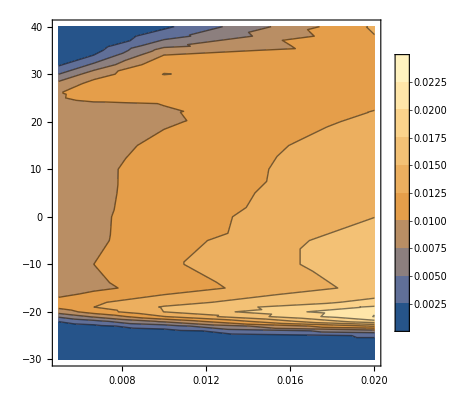

```mathematica
ListContourPlot[radiuslist,PlotLegends->Automatic]
```

```mathematica
"The hotter the star, the larger its radius."  "It would seem that the Pisani criterion is applicable. "
```

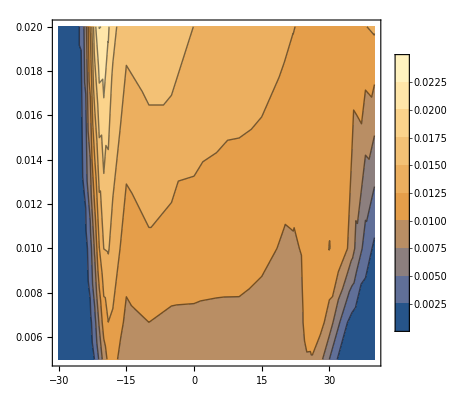

```mathematica
ListContourPlot[radiuslistrev2,PlotLegends->Automatic]
```

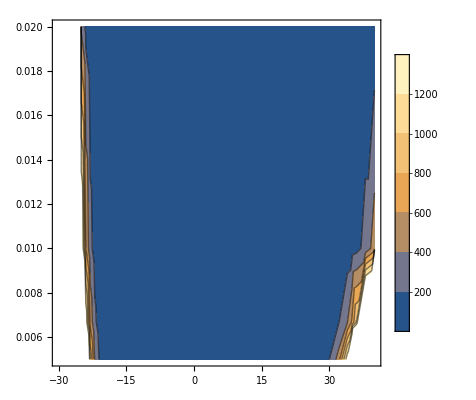

```mathematica
ListContourPlot[radiuslistrev3,PlotLegends->Automatic]
```

```mathematica
"chandrasekhar limit ¿?"
```

```mathematica
f[θ,temp]
f'[θ,temp]=0 "In θ=-20 '=∂_θ "
f''[θ,temp]>0"In θ=-20"
```

```mathematica
phase=-Graphics-;
```

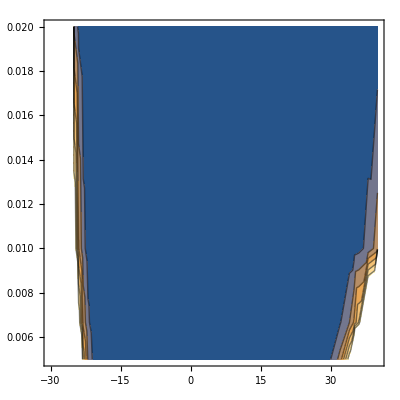
```mathematica
Show[-Graphics-,-Graphics-]
```

-Graphics-

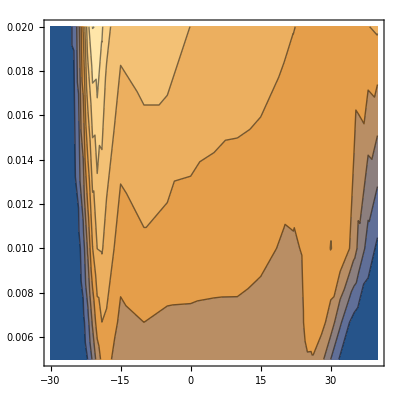
```mathematica
Show[-Graphics-,-Graphics-]
```

-Graphics-

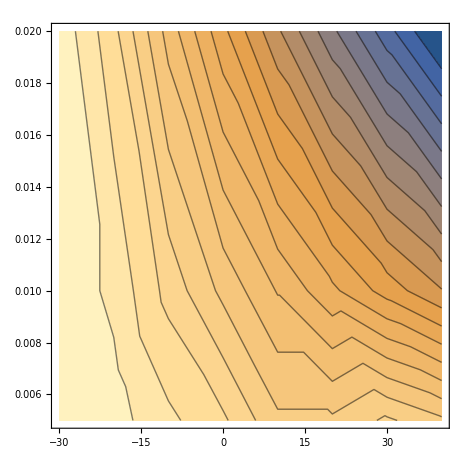
```mathematica
Show[-Graphics-,-Graphics-,PlotRange->{{-30,0},Automatic}]
```

-Graphics-

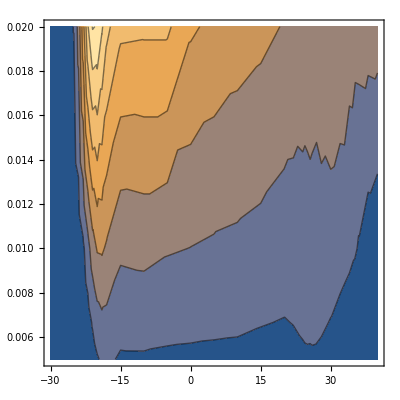
```mathematica
Show[-Graphics-,-Graphics-]
```

-Graphics-

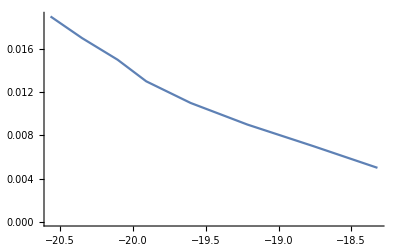
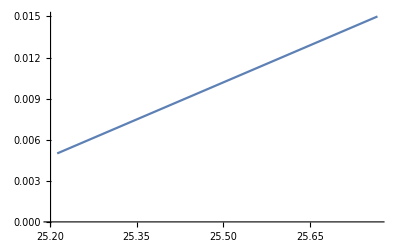
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-]
```

-Graphics-

```mathematica
Table[radiuslist[[i]],{i,1,29}]
```

{{1/50,-30,0.0000182604},{1/50,-25,0.00272832},{1/50,-24,0.00647301},{1/50,-23,0.0127442},{1/50,-22,0.0192545},{1/50,-21,0.0225826},{1/50,-20,0.0223501},{1/50,-19,0.0203572},{1/50,-18,0.0181775},{1/50,-15,0.0158153},{1/50,-10,0.0165989},{1/50,-5,0.0165989},{1/50,0,0.0149514},{1/50,5,0.014347},{1/50,10,0.0139761},{1/50,15,0.0137627},{1/50,20,0.0130423},{1/50,22,0.0125893},{1/50,24,0.0121339},{1/50,26,0.0117556},{1/50,28,0.0115126},{1/50,25,0.0119309},{1/50,30,0.0114326},{1/50,32,0.0115138},{1/50,34,0.0117327},{1/50,36,0.0120539},{1/50,38,0.0124355},{1/50,35,0.011883},{1/50,40,0.0128367}}

```mathematica
ListPointPlot3D[Table[radiuslist[[i]],{i,1,29}]]
```

-Graphics3D-

```mathematica
Table[radiuslist[[i]],{i,30,58}]
```

{{1/100,-30,3.65821×10^-6},{1/100,-25,0.000609454},{1/100,-24,0.00161416},{1/100,-23,0.00391338},{1/100,-22,0.00794289},{1/100,-21,0.0124277},{1/100,-20,0.0150217},{1/100,-19,0.0152017},{1/100,-18,0.0140624},{1/100,-15,0.0111424},{1/100,-10,0.0120714},{1/100,-5,0.011431},{1/100,0,0.011315},{1/100,5,0.0110945},{1/100,10,0.0110354},{1/100,15,0.0106603},{1/100,20,0.00968416},{1/100,22,0.00977991},{1/100,24,0.0101051},{1/100,26,0.010937},{1/100,28,0.0119173},{1/100,25,0.0104812},{1/100,30,0.0125355},{1/100,32,0.0120733},{1/100,34,0.0100249},{1/100,36,0.00687354},{1/100,38,0.00391823},{1/100,35,0.00850905},{1/100,40,0.00196966}}

```mathematica
ListPointPlot3D[Table[radiuslist[[i]],{i,30,58}]]
```

-Graphics3D-

```mathematica
"Swallow tale aparecen luego de que la estrella alcanza el radio máximo por lo que tiene que ver con el colapso de la misma."
```

```mathematica
"Large densities or large chemical potential, the interacting particles are very close to each other -> uncertainty principle"
```

## Mass radius analysis

```mathematica
radiusvsmass={{mtemp1tm30,rtemp1tm30},{mtemp1tm25,rtemp1tm25},{mtemp1tm24,rtemp1tm24},{mtemp1tm23,rtemp1tm23},{mtemp1tm22,rtemp1tm22},{mtemp1tm21,rtemp1tm21},{mtemp1tm20,rtemp1tm20},{mtemp1tm19,rtemp1tm19},{mtemp1tm18,rtemp1tm18},{mtemp1tm15,rtemp1tm15},{mtemp1tm10,rtemp1tm10},{mtemp1tm5,rtemp1tm5},{mtemp1t0,rtemp1t0},{mtemp1t5,rtemp1t5},{mtemp1t10,rtemp1t10},{mtemp1t15,rtemp1t15},{mtemp1t20,rtemp1t20},{mtemp1t22,rtemp1t22},{mtemp1t24,rtemp1t24},{mtemp1t26,rtemp1t26},{mtemp1t28,rtemp1t28},{mtemp1t25,rtemp1t25},{mtemp1t30,rtemp1t30},{mtemp1t32,rtemp1t32},{mtemp1t34,rtemp1t34},{mtemp1t36,rtemp1t36},{mtemp1t38,rtemp1t38},{mtemp1t35,rtemp1t35},{mtemp1t40,rtemp1t40},

{mtemp2tm30,rtemp2tm30},{mtemp2tm25,rtemp2tm25},{mtemp2tm24,rtemp2tm24},{mtemp2tm23,rtemp2tm23},{mtemp2tm22,rtemp2tm22},{mtemp2tm21,rtemp2tm21},{mtemp2tm20,rtemp2tm20},{mtemp2tm19,rtemp2tm19},{mtemp2tm18,rtemp2tm18},{mtemp2tm15,rtemp2tm15},{mtemp2tm10,rtemp2tm10},{mtemp2tm5,rtemp2tm5},{mtemp2t0,rtemp2t0},{mtemp2t5,rtemp2t5},{mtemp2t10,rtemp2t10},{mtemp2t15,rtemp2t15},{mtemp2t20,rtemp2t20},{mtemp2t22,rtemp2t22},{mtemp2t24,rtemp2t24},{mtemp2t26,rtemp2t26},{mtemp2t28,rtemp2t28},{mtemp2t25,rtemp2t25},{mtemp2t30,rtemp2t30},{mtemp2t32,rtemp2t32},{mtemp2t34,rtemp2t34},{mtemp2t36,rtemp2t36},{mtemp2t38,rtemp2t38},{mtemp2t35,rtemp2t35},{mtemp2t40,rtemp2t40},

{mtemp3tm30,rtemp3tm30},{mtemp3tm25,rtemp3tm25},{mtemp3tm24,rtemp3tm24},{mtemp3tm23,rtemp3tm23},{mtemp3tm22,rtemp3tm22},{mtemp3tm21,rtemp3tm21},{mtemp3tm20,rtemp3tm20},{mtemp3tm19,rtemp3tm19},{mtemp3tm18,rtemp3tm18},{mtemp3tm15,rtemp3tm15},{mtemp3tm10,rtemp3tm10},{mtemp3tm5,rtemp3tm5},{mtemp3t0,rtemp3t0},{mtemp3t5,rtemp3t5},{mtemp3t10,rtemp3t10},{mtemp3t15,rtemp3t15},{mtemp3t20,rtemp3t20},{mtemp3t22,rtemp3t22},{mtemp3t24,rtemp3t24},{mtemp3t26,rtemp3t26},{mtemp3t28,rtemp3t28},{mtemp3t25,rtemp3t25},{mtemp3t30,rtemp3t30},{mtemp3t32,rtemp3t32},{mtemp3t34,rtemp3t34},{mtemp3t36,rtemp3t36},{mtemp3t38,rtemp3t38},{mtemp3t35,rtemp3t35},{mtemp3t40,rtemp3t40},

{mtemp4tm30,rtemp4tm30},{mtemp4tm25,rtemp4tm25},{mtemp4tm24,rtemp4tm24},{mtemp4tm23,rtemp4tm23},{mtemp4tm22,rtemp4tm22},{mtemp4tm21,rtemp4tm21},{mtemp4tm20,rtemp4tm20},{mtemp4tm19,rtemp4tm19},{mtemp4tm18,rtemp4tm18},{mtemp4tm15,rtemp4tm15},{mtemp4tm10,rtemp4tm10},{mtemp4tm5,rtemp4tm5},{mtemp4t0,rtemp4t0},{mtemp4t5,rtemp4t5},{mtemp4t10,rtemp4t10},{mtemp4t15,rtemp4t15},{mtemp4t20,rtemp4t20},{mtemp4t22,rtemp4t22},{mtemp4t24,rtemp4t24},{mtemp4t26,rtemp4t26},{mtemp4t28,rtemp4t28},{mtemp4t25,rtemp4t25},{mtemp4t30,rtemp4t30},{mtemp4t32,rtemp4t32},{mtemp4t34,rtemp4t34},{mtemp4t36,rtemp4t36},{mtemp4t38,rtemp4t38},{mtemp4t35,rtemp4t35},{mtemp4t40,rtemp4t40}};
```

```mathematica
radiusvsmass
```

{{7.6695×10^-6,0.0000182604},{0.0010271,0.00272832},{0.0023861,0.00647301},{0.0046254,0.0127442},{0.00692491,0.0192545},{0.00806925,0.0225826},{0.00792127,0.0223501},{0.00713483,0.0203572},{0.00628501,0.0181775},{0.00523297,0.0158153},{0.00517226,0.0165989},{0.00517226,0.0165989},{0.00414629,0.0149514},{0.00376837,0.014347},{0.00348586,0.0139761},{0.00326402,0.0137627},{0.00294227,0.0130423},{0.0027858,0.0125893},{0.00263589,0.0121339},{0.00250935,0.0117556},{0.00241704,0.0115126},{0.00256888,0.0119309},{0.00236254,0.0114326},{0.00234318,0.0115138},{0.00235212,0.0117327},{0.00238057,0.0120539},{0.00241905,0.0124355},{0.0023645,0.011883},{0.00245886,0.0128367},{9.32857×10^-7,3.65821×10^-6},{0.000133683,0.000609454},{0.0003435,0.00161416},{0.000812389,0.00391338},{0.00162676,0.00794289},{0.00254317,0.0124277},{0.00308713,0.0150217},{0.00312707,0.0152017},{0.00287859,0.0140624},{0.00220604,0.0111424},{0.00229173,0.0120714},{0.00208535,0.011431},{0.00198672,0.011315},{0.00187772,0.0110945},{0.00180201,0.0110354},{0.00167697,0.0106603},{0.00147357,0.00968416},{0.00145722,0.00977991},{0.00150932,0.0101051},{0.00161809,0.010937},{0.00174103,0.0119173},{0.00155842,0.0104812},{0.00179894,0.0125355},{0.00169193,0.0120733},{0.00136807,0.0100249},{0.000917663,0.00687354},{0.00051742,0.00391823},{0.00114728,0.00850905},{0.000260111,0.00196966},{2.73555×10^-7,1.51974×10^-6},{0.0000398685,0.000260497},{0.000105102,0.000710489},{0.000264142,0.00184099},{0.000595219,0.00423692},{0.00109959,0.00787119},{0.00156711,0.0111387},{0.00177215,0.0124882},{0.0017279,0.0121451},{0.00130598,0.00939507},{0.00134286,0.00999922},{0.00125216,0.0095923},{0.0012116,0.00955168},{0.00116741,0.00945794},{0.00113444,0.00944735},{0.00103986,0.00891997},{0.000965658,0.00845268},{0.00102021,0.00897387},{0.00111926,0.00991265},{0.00120779,0.0108352},{0.00118096,0.0108302},{0.00117023,0.0104203},{0.000942473,0.00889094},{0.000565096,0.00544604},{0.000259847,0.00251023},{0.000102454,0.000976367},{0.0000380233,0.000354898},{0.00016503,0.00158565},{0.0000140502,0.000128235},{1.14939×10^-7,8.2838×10^-7},{0.0000168413,0.000143535},{0.0000449061,0.000396719},{0.000115897,0.00105911},{0.000277008,0.00259965},{0.000566062,0.00537605},{0.000909202,0.00859217},{0.0011329,0.0105764},{0.0011707,0.010841},{0.000898047,0.0084355},{0.000901213,0.00873323},{0.000856535,0.00847845},{0.000834668,0.00845494},{0.000813508,0.00842051},{0.000793876,0.00840535},{0.000721266,0.00782346},{0.000714672,0.00784092},{0.000783154,0.00862111},{0.000862991,0.00958514},{0.000873033,0.00988619},{0.00071323,0.00831149},{0.00088363,0.00989502},{0.000418533,0.00498721},{0.000178094,0.00211987},{0.0000630537,0.000735176},{0.0000209221,0.000237102},{6.9118×10^-6,0.0000760349},{0.0000364358,0.000418986},{2.37644×10^-6,0.0000254044}}

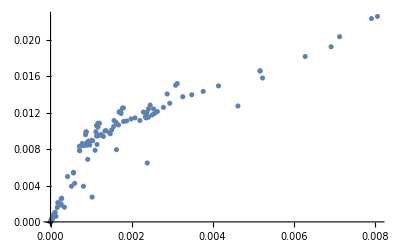

```mathematica
ListPlot[%1430]
```

```mathematica
radiusvsmassrev=Table[{radiusvsmass[[i,2]],radiusvsmass[[i,1]]},{i,1,20}];
```

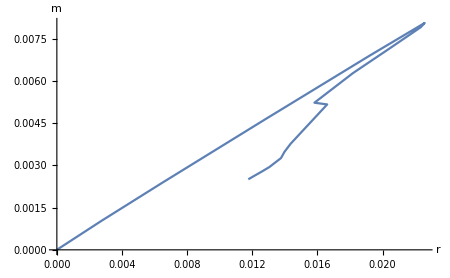

```mathematica
ListPlot[radiusvsmassrev,AxesLabel->{"r","m"},Joined->True]
```

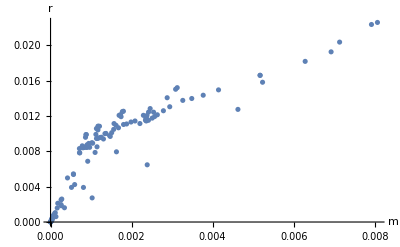

```mathematica
ListPlot[radiusvsmass,AxesLabel->{"m","r"}]
```

```mathematica
mlist={{1/50,-30,mtemp1tm30},{1/50,-25,mtemp1tm25},{1/50,-24,mtemp1tm24},{1/50,-23,mtemp1tm23},{1/50,-22,mtemp1tm22},{1/50,-21,mtemp1tm21},{1/50,-20,mtemp1tm20},{1/50,-19,mtemp1tm19},{1/50,-18,mtemp1tm18},{1/50,-15,mtemp1tm15},{1/50,-10,mtemp1tm10},{1/50,-5,mtemp1tm5},{1/50,0,mtemp1t0},{1/50,5,mtemp1t5},{1/50,10,mtemp1t10},{1/50,15,mtemp1t15},{1/50,20,mtemp1t20},{1/50,22,mtemp1t22},{1/50,24,mtemp1t24},{1/50,26,mtemp1t26},{1/50,28,mtemp1t28},{1/50,25,mtemp1t25},{1/50,30,mtemp1t30},{1/50,32,mtemp1t32},{1/50,34,mtemp1t34},{1/50,36,mtemp1t36},{1/50,38,mtemp1t38},{1/50,35,mtemp1t35},{1/50,40,mtemp1t40},

{1/100,-30,mtemp2tm30},{1/100,-25,mtemp2tm25},{1/100,-24,mtemp2tm24},{1/100,-23,mtemp2tm23},{1/100,-22,mtemp2tm22},{1/100,-21,mtemp2tm21},{1/100,-20,mtemp2tm20},{1/100,-19,mtemp2tm19},{1/100,-18,mtemp2tm18},{1/100,-15,mtemp2tm15},{1/100,-10,mtemp2tm10},{1/100,-5,mtemp2tm5},{1/100,0,mtemp2t0},{1/100,5,mtemp2t5},{1/100,10,mtemp2t10},{1/100,15,mtemp2t15},{1/100,20,mtemp2t20},{1/100,22,mtemp2t22},{1/100,24,mtemp2t24},{1/100,26,mtemp2t26},{1/100,28,mtemp2t28},{1/100,25,mtemp2t25},{1/100,30,mtemp2t30},{1/100,32,mtemp2t32},{1/100,34,mtemp2t34},{1/100,36,mtemp2t36},{1/100,38,mtemp2t38},{1/100,35,mtemp2t35},{1/100,40,mtemp2t40},

{1/150,-30,mtemp3tm30},{1/150,-25,mtemp3tm25},{1/150,-24,mtemp3tm24},{1/150,-23,mtemp3tm23},{1/150,-22,mtemp3tm22},{1/150,-21,mtemp3tm21},{1/150,-20,mtemp3tm20},{1/150,-19,mtemp3tm19},{1/150,-18,mtemp3tm18},{1/150,-15,mtemp3tm15},{1/150,-10,mtemp3tm10},{1/150,-5,mtemp3tm5},{1/150,0,mtemp3t0},{1/150,5,mtemp3t5},{1/150,10,mtemp3t10},{1/150,15,mtemp3t15},{1/150,20,mtemp3t20},{1/150,22,mtemp3t22},{1/150,24,mtemp3t24},{1/150,26,mtemp3t26},{1/150,28,mtemp3t28},{1/150,25,mtemp3t25},{1/150,30,mtemp3t30},{1/150,32,mtemp3t32},{1/150,34,mtemp3t34},{1/150,36,mtemp3t36},{1/150,38,mtemp3t38},{1/150,35,mtemp3t35},{1/150,40,mtemp3t40},

{1/200,-30,mtemp4tm30},{1/200,-25,mtemp4tm25},{1/200,-24,mtemp4tm24},{1/200,-23,mtemp4tm23},{1/200,-22,mtemp4tm22},{1/200,-21,mtemp4tm21},{1/200,-20,mtemp4tm20},{1/200,-19,mtemp4tm19},{1/200,-18,mtemp4tm18},{1/200,-15,mtemp4tm15},{1/200,-10,mtemp4tm10},{1/200,-5,mtemp4tm5},{1/200,0,mtemp4t0},{1/200,5,mtemp4t5},{1/200,10,mtemp4t10},{1/200,15,mtemp4t15},{1/200,20,mtemp4t20},{1/200,22,mtemp4t22},{1/200,24,mtemp4t24},{1/200,26,mtemp4t26},{1/200,28,mtemp4t28},{1/200,25,mtemp4t25},{1/200,30,mtemp4t30},{1/200,32,mtemp4t32},{1/200,34,mtemp4t34},{1/200,36,mtemp4t36},{1/200,38,mtemp4t38},{1/200,35,mtemp4t35},{1/200,40,mtemp4t40}};
```

```mathematica
mlistrev2=Table[{mlist[[i,2]],mlist[[i,1]],mlist[[i,3]]},{i,1,Length[radiuslist]}]
```

{{-30,1/50,7.6695×10^-6},{-25,1/50,0.0010271},{-24,1/50,0.0023861},{-23,1/50,0.0046254},{-22,1/50,0.00692491},{-21,1/50,0.00806925},{-20,1/50,0.00792127},{-19,1/50,0.00713483},{-18,1/50,0.00628501},{-15,1/50,0.00523297},{-10,1/50,0.00517226},{-5,1/50,0.00517226},{0,1/50,0.00414629},{5,1/50,0.00376837},{10,1/50,0.00348586},{15,1/50,0.00326402},{20,1/50,0.00294227},{22,1/50,0.0027858},{24,1/50,0.00263589},{26,1/50,0.00250935},{28,1/50,0.00241704},{25,1/50,0.00256888},{30,1/50,0.00236254},{32,1/50,0.00234318},{34,1/50,0.00235212},{36,1/50,0.00238057},{38,1/50,0.00241905},{35,1/50,0.0023645},{40,1/50,0.00245886},{-30,1/100,9.32857×10^-7},{-25,1/100,0.000133683},{-24,1/100,0.0003435},{-23,1/100,0.000812389},{-22,1/100,0.00162676},{-21,1/100,0.00254317},{-20,1/100,0.00308713},{-19,1/100,0.00312707},{-18,1/100,0.00287859},{-15,1/100,0.00220604},{-10,1/100,0.00229173},{-5,1/100,0.00208535},{0,1/100,0.00198672},{5,1/100,0.00187772},{10,1/100,0.00180201},{15,1/100,0.00167697},{20,1/100,0.00147357},{22,1/100,0.00145722},{24,1/100,0.00150932},{26,1/100,0.00161809},{28,1/100,0.00174103},{25,1/100,0.00155842},{30,1/100,0.00179894},{32,1/100,0.00169193},{34,1/100,0.00136807},{36,1/100,0.000917663},{38,1/100,0.00051742},{35,1/100,0.00114728},{40,1/100,0.000260111},{-30,1/150,2.73555×10^-7},{-25,1/150,0.0000398685},{-24,1/150,0.000105102},{-23,1/150,0.000264142},{-22,1/150,0.000595219},{-21,1/150,0.00109959},{-20,1/150,0.00156711},{-19,1/150,0.00177215},{-18,1/150,0.0017279},{-15,1/150,0.00130598},{-10,1/150,0.00134286},{-5,1/150,0.00125216},{0,1/150,0.0012116},{5,1/150,0.00116741},{10,1/150,0.00113444},{15,1/150,0.00103986},{20,1/150,0.000965658},{22,1/150,0.00102021},{24,1/150,0.00111926},{26,1/150,0.00120779},{28,1/150,0.00118096},{25,1/150,0.00117023},{30,1/150,0.000942473},{32,1/150,0.000565096},{34,1/150,0.000259847},{36,1/150,0.000102454},{38,1/150,0.0000380233},{35,1/150,0.00016503},{40,1/150,0.0000140502},{-30,1/200,1.14939×10^-7},{-25,1/200,0.0000168413},{-24,1/200,0.0000449061},{-23,1/200,0.000115897},{-22,1/200,0.000277008},{-21,1/200,0.000566062},{-20,1/200,0.000909202},{-19,1/200,0.0011329},{-18,1/200,0.0011707},{-15,1/200,0.000898047},{-10,1/200,0.000901213},{-5,1/200,0.000856535},{0,1/200,0.000834668},{5,1/200,0.000813508},{10,1/200,0.000793876},{15,1/200,0.000721266},{20,1/200,0.000714672},{22,1/200,0.000783154},{24,1/200,0.000862991},{26,1/200,0.000873033},{28,1/200,0.00071323},{25,1/200,0.00088363},{30,1/200,0.000418533},{32,1/200,0.000178094},{34,1/200,0.0000630537},{36,1/200,0.0000209221},{38,1/200,6.9118×10^-6},{35,1/200,0.0000364358},{40,1/200,2.37644×10^-6}}

```mathematica
Interpolation[mlistrev2]
```

InterpolatingFunction[…]

```mathematica
Plot3D[%[x,y],{x,-30.,40.},{y,0.005,0.02}]
```

-Graphics3D-

```mathematica
Table[{mlist[[i,1]],mlist[[i,3]]},{i,1,Length[radiuslist]}]
```

{{1/50,7.6695×10^-6},{1/50,0.0010271},{1/50,0.0023861},{1/50,0.0046254},{1/50,0.00692491},{1/50,0.00806925},{1/50,0.00792127},{1/50,0.00713483},{1/50,0.00628501},{1/50,0.00523297},{1/50,0.00517226},{1/50,0.00517226},{1/50,0.00414629},{1/50,0.00376837},{1/50,0.00348586},{1/50,0.00326402},{1/50,0.00294227},{1/50,0.0027858},{1/50,0.00263589},{1/50,0.00250935},{1/50,0.00241704},{1/50,0.00256888},{1/50,0.00236254},{1/50,0.00234318},{1/50,0.00235212},{1/50,0.00238057},{1/50,0.00241905},{1/50,0.0023645},{1/50,0.00245886},{1/100,9.32857×10^-7},{1/100,0.000133683},{1/100,0.0003435},{1/100,0.000812389},{1/100,0.00162676},{1/100,0.00254317},{1/100,0.00308713},{1/100,0.00312707},{1/100,0.00287859},{1/100,0.00220604},{1/100,0.00229173},{1/100,0.00208535},{1/100,0.00198672},{1/100,0.00187772},{1/100,0.00180201},{1/100,0.00167697},{1/100,0.00147357},{1/100,0.00145722},{1/100,0.00150932},{1/100,0.00161809},{1/100,0.00174103},{1/100,0.00155842},{1/100,0.00179894},{1/100,0.00169193},{1/100,0.00136807},{1/100,0.000917663},{1/100,0.00051742},{1/100,0.00114728},{1/100,0.000260111},{1/150,2.73555×10^-7},{1/150,0.0000398685},{1/150,0.000105102},{1/150,0.000264142},{1/150,0.000595219},{1/150,0.00109959},{1/150,0.00156711},{1/150,0.00177215},{1/150,0.0017279},{1/150,0.00130598},{1/150,0.00134286},{1/150,0.00125216},{1/150,0.0012116},{1/150,0.00116741},{1/150,0.00113444},{1/150,0.00103986},{1/150,0.000965658},{1/150,0.00102021},{1/150,0.00111926},{1/150,0.00120779},{1/150,0.00118096},{1/150,0.00117023},{1/150,0.000942473},{1/150,0.000565096},{1/150,0.000259847},{1/150,0.000102454},{1/150,0.0000380233},{1/150,0.00016503},{1/150,0.0000140502},{1/200,1.14939×10^-7},{1/200,0.0000168413},{1/200,0.0000449061},{1/200,0.000115897},{1/200,0.000277008},{1/200,0.000566062},{1/200,0.000909202},{1/200,0.0011329},{1/200,0.0011707},{1/200,0.000898047},{1/200,0.000901213},{1/200,0.000856535},{1/200,0.000834668},{1/200,0.000813508},{1/200,0.000793876},{1/200,0.000721266},{1/200,0.000714672},{1/200,0.000783154},{1/200,0.000862991},{1/200,0.000873033},{1/200,0.00071323},{1/200,0.00088363},{1/200,0.000418533},{1/200,0.000178094},{1/200,0.0000630537},{1/200,0.0000209221},{1/200,6.9118×10^-6},{1/200,0.0000364358},{1/200,2.37644×10^-6}}

```mathematica
stab1=Table[{mlist[[i,2]],mlist[[i,3]]},{i,1,29}]
```

{{-30,7.6695×10^-6},{-25,0.0010271},{-24,0.0023861},{-23,0.0046254},{-22,0.00692491},{-21,0.00806925},{-20,0.00792127},{-19,0.00713483},{-18,0.00628501},{-15,0.00523297},{-10,0.00517226},{-5,0.00517226},{0,0.00414629},{5,0.00376837},{10,0.00348586},{15,0.00326402},{20,0.00294227},{22,0.0027858},{24,0.00263589},{26,0.00250935},{28,0.00241704},{25,0.00256888},{30,0.00236254},{32,0.00234318},{34,0.00235212},{36,0.00238057},{38,0.00241905},{35,0.0023645},{40,0.00245886}}

```mathematica
stab2=Table[{mlist[[i,2]],mlist[[i,3]]},{i,30,58}]
```

{{-30,9.32857×10^-7},{-25,0.000133683},{-24,0.0003435},{-23,0.000812389},{-22,0.00162676},{-21,0.00254317},{-20,0.00308713},{-19,0.00312707},{-18,0.00287859},{-15,0.00220604},{-10,0.00229173},{-5,0.00208535},{0,0.00198672},{5,0.00187772},{10,0.00180201},{15,0.00167697},{20,0.00147357},{22,0.00145722},{24,0.00150932},{26,0.00161809},{28,0.00174103},{25,0.00155842},{30,0.00179894},{32,0.00169193},{34,0.00136807},{36,0.000917663},{38,0.00051742},{35,0.00114728},{40,0.000260111}}

```mathematica
stab3=Table[{mlist[[i,2]],mlist[[i,3]]},{i,59,59+28}]
```

{{-30,2.73555×10^-7},{-25,0.0000398685},{-24,0.000105102},{-23,0.000264142},{-22,0.000595219},{-21,0.00109959},{-20,0.00156711},{-19,0.00177215},{-18,0.0017279},{-15,0.00130598},{-10,0.00134286},{-5,0.00125216},{0,0.0012116},{5,0.00116741},{10,0.00113444},{15,0.00103986},{20,0.000965658},{22,0.00102021},{24,0.00111926},{26,0.00120779},{28,0.00118096},{25,0.00117023},{30,0.000942473},{32,0.000565096},{34,0.000259847},{36,0.000102454},{38,0.0000380233},{35,0.00016503},{40,0.0000140502}}

```mathematica
stab4=Table[{mlist[[i,2]],mlist[[i,3]]},{i,59+28,59+28+28}]
```

{{40,0.0000140502},{-30,1.14939×10^-7},{-25,0.0000168413},{-24,0.0000449061},{-23,0.000115897},{-22,0.000277008},{-21,0.000566062},{-20,0.000909202},{-19,0.0011329},{-18,0.0011707},{-15,0.000898047},{-10,0.000901213},{-5,0.000856535},{0,0.000834668},{5,0.000813508},{10,0.000793876},{15,0.000721266},{20,0.000714672},{22,0.000783154},{24,0.000862991},{26,0.000873033},{28,0.00071323},{25,0.00088363},{30,0.000418533},{32,0.000178094},{34,0.0000630537},{36,0.0000209221},{38,6.9118×10^-6},{35,0.0000364358}}

```mathematica
Hue[0,1,1]
```

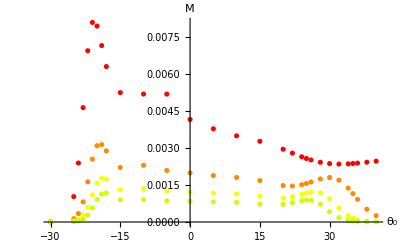

```mathematica
ListPlot[{stab1,stab2,stab3,stab4},AxesLabel->{"θ_0","M"},PlotStyle->{Hue[0,1,1],Hue[0.09,1,1],Hue[0.17,1,1],Hue[.2,1,1]}]
```

```mathematica
ListPlot[Table[{FindRoot[D[InterpolatingFunction[…][x,y],x]==0,{x,-20}][[1,2]],y},{y,1/200,1/50,1/500}],Joined->True]
```

-Graphics-

```mathematica
ListPlot[Table[{FindRoot[D[InterpolatingFunction[…][x,y],x]==0,{x,28}][[1,2]],y},{y,1/200,1/50,1/100}],Joined->True]
```

-Graphics-

```mathematica
mlistrev2
```

{{-30,1/50,7.6695×10^-6},{-25,1/50,0.0010271},{-24,1/50,0.0023861},{-23,1/50,0.0046254},{-22,1/50,0.00692491},{-21,1/50,0.00806925},{-20,1/50,0.00792127},{-19,1/50,0.00713483},{-18,1/50,0.00628501},{-15,1/50,0.00523297},{-10,1/50,0.00517226},{-5,1/50,0.00517226},{0,1/50,0.00414629},{5,1/50,0.00376837},{10,1/50,0.00348586},{15,1/50,0.00326402},{20,1/50,0.00294227},{22,1/50,0.0027858},{24,1/50,0.00263589},{26,1/50,0.00250935},{28,1/50,0.00241704},{25,1/50,0.00256888},{30,1/50,0.00236254},{32,1/50,0.00234318},{34,1/50,0.00235212},{36,1/50,0.00238057},{38,1/50,0.00241905},{35,1/50,0.0023645},{40,1/50,0.00245886},{-30,1/100,9.32857×10^-7},{-25,1/100,0.000133683},{-24,1/100,0.0003435},{-23,1/100,0.000812389},{-22,1/100,0.00162676},{-21,1/100,0.00254317},{-20,1/100,0.00308713},{-19,1/100,0.00312707},{-18,1/100,0.00287859},{-15,1/100,0.00220604},{-10,1/100,0.00229173},{-5,1/100,0.00208535},{0,1/100,0.00198672},{5,1/100,0.00187772},{10,1/100,0.00180201},{15,1/100,0.00167697},{20,1/100,0.00147357},{22,1/100,0.00145722},{24,1/100,0.00150932},{26,1/100,0.00161809},{28,1/100,0.00174103},{25,1/100,0.00155842},{30,1/100,0.00179894},{32,1/100,0.00169193},{34,1/100,0.00136807},{36,1/100,0.000917663},{38,1/100,0.00051742},{35,1/100,0.00114728},{40,1/100,0.000260111},{-30,1/150,2.73555×10^-7},{-25,1/150,0.0000398685},{-24,1/150,0.000105102},{-23,1/150,0.000264142},{-22,1/150,0.000595219},{-21,1/150,0.00109959},{-20,1/150,0.00156711},{-19,1/150,0.00177215},{-18,1/150,0.0017279},{-15,1/150,0.00130598},{-10,1/150,0.00134286},{-5,1/150,0.00125216},{0,1/150,0.0012116},{5,1/150,0.00116741},{10,1/150,0.00113444},{15,1/150,0.00103986},{20,1/150,0.000965658},{22,1/150,0.00102021},{24,1/150,0.00111926},{26,1/150,0.00120779},{28,1/150,0.00118096},{25,1/150,0.00117023},{30,1/150,0.000942473},{32,1/150,0.000565096},{34,1/150,0.000259847},{36,1/150,0.000102454},{38,1/150,0.0000380233},{35,1/150,0.00016503},{40,1/150,0.0000140502},{-30,1/200,1.14939×10^-7},{-25,1/200,0.0000168413},{-24,1/200,0.0000449061},{-23,1/200,0.000115897},{-22,1/200,0.000277008},{-21,1/200,0.000566062},{-20,1/200,0.000909202},{-19,1/200,0.0011329},{-18,1/200,0.0011707},{-15,1/200,0.000898047},{-10,1/200,0.000901213},{-5,1/200,0.000856535},{0,1/200,0.000834668},{5,1/200,0.000813508},{10,1/200,0.000793876},{15,1/200,0.000721266},{20,1/200,0.000714672},{22,1/200,0.000783154},{24,1/200,0.000862991},{26,1/200,0.000873033},{28,1/200,0.00071323},{25,1/200,0.00088363},{30,1/200,0.000418533},{32,1/200,0.000178094},{34,1/200,0.0000630537},{36,1/200,0.0000209221},{38,1/200,6.9118×10^-6},{35,1/200,0.0000364358},{40,1/200,2.37644×10^-6}}

```mathematica
mlistrev3=Table[{mlist[[i,2]],mlist[[i,3]],mlist[[i,1]]},{i,1,Length[radiuslist]}]
```

{{-30,7.6695×10^-6,1/50},{-25,0.0010271,1/50},{-24,0.0023861,1/50},{-23,0.0046254,1/50},{-22,0.00692491,1/50},{-21,0.00806925,1/50},{-20,0.00792127,1/50},{-19,0.00713483,1/50},{-18,0.00628501,1/50},{-15,0.00523297,1/50},{-10,0.00517226,1/50},{-5,0.00517226,1/50},{0,0.00414629,1/50},{5,0.00376837,1/50},{10,0.00348586,1/50},{15,0.00326402,1/50},{20,0.00294227,1/50},{22,0.0027858,1/50},{24,0.00263589,1/50},{26,0.00250935,1/50},{28,0.00241704,1/50},{25,0.00256888,1/50},{30,0.00236254,1/50},{32,0.00234318,1/50},{34,0.00235212,1/50},{36,0.00238057,1/50},{38,0.00241905,1/50},{35,0.0023645,1/50},{40,0.00245886,1/50},{-30,9.32857×10^-7,1/100},{-25,0.000133683,1/100},{-24,0.0003435,1/100},{-23,0.000812389,1/100},{-22,0.00162676,1/100},{-21,0.00254317,1/100},{-20,0.00308713,1/100},{-19,0.00312707,1/100},{-18,0.00287859,1/100},{-15,0.00220604,1/100},{-10,0.00229173,1/100},{-5,0.00208535,1/100},{0,0.00198672,1/100},{5,0.00187772,1/100},{10,0.00180201,1/100},{15,0.00167697,1/100},{20,0.00147357,1/100},{22,0.00145722,1/100},{24,0.00150932,1/100},{26,0.00161809,1/100},{28,0.00174103,1/100},{25,0.00155842,1/100},{30,0.00179894,1/100},{32,0.00169193,1/100},{34,0.00136807,1/100},{36,0.000917663,1/100},{38,0.00051742,1/100},{35,0.00114728,1/100},{40,0.000260111,1/100},{-30,2.73555×10^-7,1/150},{-25,0.0000398685,1/150},{-24,0.000105102,1/150},{-23,0.000264142,1/150},{-22,0.000595219,1/150},{-21,0.00109959,1/150},{-20,0.00156711,1/150},{-19,0.00177215,1/150},{-18,0.0017279,1/150},{-15,0.00130598,1/150},{-10,0.00134286,1/150},{-5,0.00125216,1/150},{0,0.0012116,1/150},{5,0.00116741,1/150},{10,0.00113444,1/150},{15,0.00103986,1/150},{20,0.000965658,1/150},{22,0.00102021,1/150},{24,0.00111926,1/150},{26,0.00120779,1/150},{28,0.00118096,1/150},{25,0.00117023,1/150},{30,0.000942473,1/150},{32,0.000565096,1/150},{34,0.000259847,1/150},{36,0.000102454,1/150},{38,0.0000380233,1/150},{35,0.00016503,1/150},{40,0.0000140502,1/150},{-30,1.14939×10^-7,1/200},{-25,0.0000168413,1/200},{-24,0.0000449061,1/200},{-23,0.000115897,1/200},{-22,0.000277008,1/200},{-21,0.000566062,1/200},{-20,0.000909202,1/200},{-19,0.0011329,1/200},{-18,0.0011707,1/200},{-15,0.000898047,1/200},{-10,0.000901213,1/200},{-5,0.000856535,1/200},{0,0.000834668,1/200},{5,0.000813508,1/200},{10,0.000793876,1/200},{15,0.000721266,1/200},{20,0.000714672,1/200},{22,0.000783154,1/200},{24,0.000862991,1/200},{26,0.000873033,1/200},{28,0.00071323,1/200},{25,0.00088363,1/200},{30,0.000418533,1/200},{32,0.000178094,1/200},{34,0.0000630537,1/200},{36,0.0000209221,1/200},{38,6.9118×10^-6,1/200},{35,0.0000364358,1/200},{40,2.37644×10^-6,1/200}}

```mathematica
ListPointPlot3D[mlistrev3,AxesLabel->{"θ_0","M","T"},ColorFunction->"BlueGreenYellow"]
```

-Graphics3D-

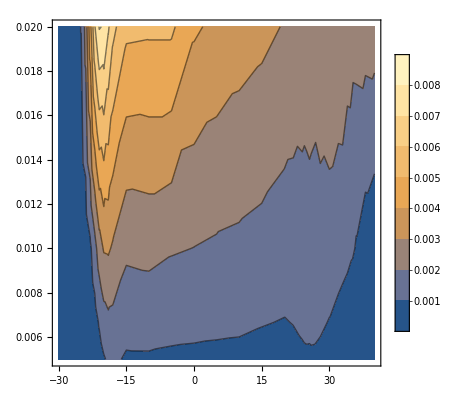

```mathematica
ListContourPlot[mlistrev2,PlotLegends->Automatic]
```

```mathematica
mvsrlist=Table[{radiuslist[[i,3]],mlist[[i,3]],mlist[[i,1]]},{i,1,29}]
```

{{0.0000182604,7.6695×10^-6,1/50},{0.00272832,0.0010271,1/50},{0.00647301,0.0023861,1/50},{0.0127442,0.0046254,1/50},{0.0192545,0.00692491,1/50},{0.0225826,0.00806925,1/50},{0.0223501,0.00792127,1/50},{0.0203572,0.00713483,1/50},{0.0181775,0.00628501,1/50},{0.0158153,0.00523297,1/50},{0.0165989,0.00517226,1/50},{0.0165989,0.00517226,1/50},{0.0149514,0.00414629,1/50},{0.014347,0.00376837,1/50},{0.0139761,0.00348586,1/50},{0.0137627,0.00326402,1/50},{0.0130423,0.00294227,1/50},{0.0125893,0.0027858,1/50},{0.0121339,0.00263589,1/50},{0.0117556,0.00250935,1/50},{0.0115126,0.00241704,1/50},{0.0119309,0.00256888,1/50},{0.0114326,0.00236254,1/50},{0.0115138,0.00234318,1/50},{0.0117327,0.00235212,1/50},{0.0120539,0.00238057,1/50},{0.0124355,0.00241905,1/50},{0.011883,0.0023645,1/50},{0.0128367,0.00245886,1/50}}

```mathematica
mvsrlist=Table[{radiuslist[[i,3]],mlist[[i,3]]},{i,1,Length[radiuslist]}]
```

{{0.0000182604,7.6695×10^-6},{0.00272832,0.0010271},{0.00647301,0.0023861},{0.0127442,0.0046254},{0.0192545,0.00692491},{0.0225826,0.00806925},{0.0223501,0.00792127},{0.0203572,0.00713483},{0.0181775,0.00628501},{0.0158153,0.00523297},{0.0165989,0.00517226},{0.0165989,0.00517226},{0.0149514,0.00414629},{0.014347,0.00376837},{0.0139761,0.00348586},{0.0137627,0.00326402},{0.0130423,0.00294227},{0.0125893,0.0027858},{0.0121339,0.00263589},{0.0117556,0.00250935},{0.0115126,0.00241704},{0.0119309,0.00256888},{0.0114326,0.00236254},{0.0115138,0.00234318},{0.0117327,0.00235212},{0.0120539,0.00238057},{0.0124355,0.00241905},{0.011883,0.0023645},{0.0128367,0.00245886},{3.65821×10^-6,9.32857×10^-7},{0.000609454,0.000133683},{0.00161416,0.0003435},{0.00391338,0.000812389},{0.00794289,0.00162676},{0.0124277,0.00254317},{0.0150217,0.00308713},{0.0152017,0.00312707},{0.0140624,0.00287859},{0.0111424,0.00220604},{0.0120714,0.00229173},{0.011431,0.00208535},{0.011315,0.00198672},{0.0110945,0.00187772},{0.0110354,0.00180201},{0.0106603,0.00167697},{0.00968416,0.00147357},{0.00977991,0.00145722},{0.0101051,0.00150932},{0.010937,0.00161809},{0.0119173,0.00174103},{0.0104812,0.00155842},{0.0125355,0.00179894},{0.0120733,0.00169193},{0.0100249,0.00136807},{0.00687354,0.000917663},{0.00391823,0.00051742},{0.00850905,0.00114728},{0.00196966,0.000260111},{1.51974×10^-6,2.73555×10^-7},{0.000260497,0.0000398685},{0.000710489,0.000105102},{0.00184099,0.000264142},{0.00423692,0.000595219},{0.00787119,0.00109959},{0.0111387,0.00156711},{0.0124882,0.00177215},{0.0121451,0.0017279},{0.00939507,0.00130598},{0.00999922,0.00134286},{0.0095923,0.00125216},{0.00955168,0.0012116},{0.00945794,0.00116741},{0.00944735,0.00113444},{0.00891997,0.00103986},{0.00845268,0.000965658},{0.00897387,0.00102021},{0.00991265,0.00111926},{0.0108352,0.00120779},{0.0108302,0.00118096},{0.0104203,0.00117023},{0.00889094,0.000942473},{0.00544604,0.000565096},{0.00251023,0.000259847},{0.000976367,0.000102454},{0.000354898,0.0000380233},{0.00158565,0.00016503},{0.000128235,0.0000140502},{8.2838×10^-7,1.14939×10^-7},{0.000143535,0.0000168413},{0.000396719,0.0000449061},{0.00105911,0.000115897},{0.00259965,0.000277008},{0.00537605,0.000566062},{0.00859217,0.000909202},{0.0105764,0.0011329},{0.010841,0.0011707},{0.0084355,0.000898047},{0.00873323,0.000901213},{0.00847845,0.000856535},{0.00845494,0.000834668},{0.00842051,0.000813508},{0.00840535,0.000793876},{0.00782346,0.000721266},{0.00784092,0.000714672},{0.00862111,0.000783154},{0.00958514,0.000862991},{0.00988619,0.000873033},{0.00831149,0.00071323},{0.00989502,0.00088363},{0.00498721,0.000418533},{0.00211987,0.000178094},{0.000735176,0.0000630537},{0.000237102,0.0000209221},{0.0000760349,6.9118×10^-6},{0.000418986,0.0000364358},{0.0000254044,2.37644×10^-6}}

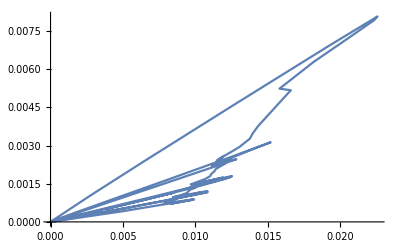

```mathematica
ListPlot[mvsrlist,Joined->True]
```

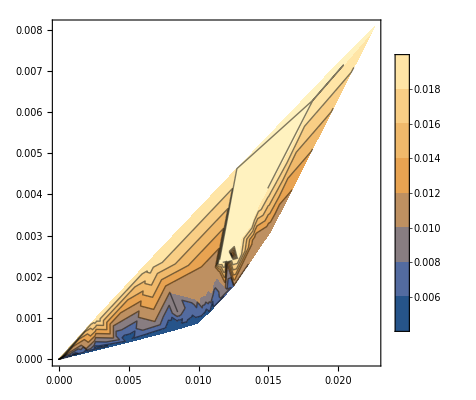

```mathematica
ListContourPlot[mvsrlist,PlotLegends->Automatic]
```

```mathematica
mvsrlist2=Table[{radiuslist[[i,3]],mlist[[i,3]],mlist[[i,2]]},{i,1,Length[radiuslist]}]
```

{{0.0000182604,7.6695×10^-6,-30},{0.00272832,0.0010271,-25},{0.00647301,0.0023861,-24},{0.0127442,0.0046254,-23},{0.0192545,0.00692491,-22},{0.0225826,0.00806925,-21},{0.0223501,0.00792127,-20},{0.0203572,0.00713483,-19},{0.0181775,0.00628501,-18},{0.0158153,0.00523297,-15},{0.0165989,0.00517226,-10},{0.0165989,0.00517226,-5},{0.0149514,0.00414629,0},{0.014347,0.00376837,5},{0.0139761,0.00348586,10},{0.0137627,0.00326402,15},{0.0130423,0.00294227,20},{0.0125893,0.0027858,22},{0.0121339,0.00263589,24},{0.0117556,0.00250935,26},{0.0115126,0.00241704,28},{0.0119309,0.00256888,25},{0.0114326,0.00236254,30},{0.0115138,0.00234318,32},{0.0117327,0.00235212,34},{0.0120539,0.00238057,36},{0.0124355,0.00241905,38},{0.011883,0.0023645,35},{0.0128367,0.00245886,40},{3.65821×10^-6,9.32857×10^-7,-30},{0.000609454,0.000133683,-25},{0.00161416,0.0003435,-24},{0.00391338,0.000812389,-23},{0.00794289,0.00162676,-22},{0.0124277,0.00254317,-21},{0.0150217,0.00308713,-20},{0.0152017,0.00312707,-19},{0.0140624,0.00287859,-18},{0.0111424,0.00220604,-15},{0.0120714,0.00229173,-10},{0.011431,0.00208535,-5},{0.011315,0.00198672,0},{0.0110945,0.00187772,5},{0.0110354,0.00180201,10},{0.0106603,0.00167697,15},{0.00968416,0.00147357,20},{0.00977991,0.00145722,22},{0.0101051,0.00150932,24},{0.010937,0.00161809,26},{0.0119173,0.00174103,28},{0.0104812,0.00155842,25},{0.0125355,0.00179894,30},{0.0120733,0.00169193,32},{0.0100249,0.00136807,34},{0.00687354,0.000917663,36},{0.00391823,0.00051742,38},{0.00850905,0.00114728,35},{0.00196966,0.000260111,40},{1.51974×10^-6,2.73555×10^-7,-30},{0.000260497,0.0000398685,-25},{0.000710489,0.000105102,-24},{0.00184099,0.000264142,-23},{0.00423692,0.000595219,-22},{0.00787119,0.00109959,-21},{0.0111387,0.00156711,-20},{0.0124882,0.00177215,-19},{0.0121451,0.0017279,-18},{0.00939507,0.00130598,-15},{0.00999922,0.00134286,-10},{0.0095923,0.00125216,-5},{0.00955168,0.0012116,0},{0.00945794,0.00116741,5},{0.00944735,0.00113444,10},{0.00891997,0.00103986,15},{0.00845268,0.000965658,20},{0.00897387,0.00102021,22},{0.00991265,0.00111926,24},{0.0108352,0.00120779,26},{0.0108302,0.00118096,28},{0.0104203,0.00117023,25},{0.00889094,0.000942473,30},{0.00544604,0.000565096,32},{0.00251023,0.000259847,34},{0.000976367,0.000102454,36},{0.000354898,0.0000380233,38},{0.00158565,0.00016503,35},{0.000128235,0.0000140502,40},{8.2838×10^-7,1.14939×10^-7,-30},{0.000143535,0.0000168413,-25},{0.000396719,0.0000449061,-24},{0.00105911,0.000115897,-23},{0.00259965,0.000277008,-22},{0.00537605,0.000566062,-21},{0.00859217,0.000909202,-20},{0.0105764,0.0011329,-19},{0.010841,0.0011707,-18},{0.0084355,0.000898047,-15},{0.00873323,0.000901213,-10},{0.00847845,0.000856535,-5},{0.00845494,0.000834668,0},{0.00842051,0.000813508,5},{0.00840535,0.000793876,10},{0.00782346,0.000721266,15},{0.00784092,0.000714672,20},{0.00862111,0.000783154,22},{0.00958514,0.000862991,24},{0.00988619,0.000873033,26},{0.00831149,0.00071323,28},{0.00989502,0.00088363,25},{0.00498721,0.000418533,30},{0.00211987,0.000178094,32},{0.000735176,0.0000630537,34},{0.000237102,0.0000209221,36},{0.0000760349,6.9118×10^-6,38},{0.000418986,0.0000364358,35},{0.0000254044,2.37644×10^-6,40}}

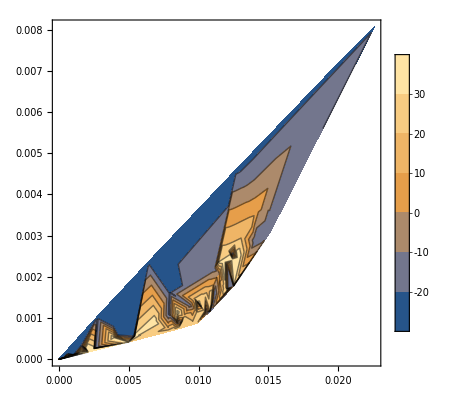

```mathematica
ListContourPlot[mvsrlist2,PlotLegends->Automatic]
```

## Derivative analysis

### Temperaturas estudiadas

### Temp1={{1*10^(-2),1.5*10^(-2),2*10^(-2),2.5*10^(-2),3*10^(-2),3.5*10^(-2),4*10^(-2),4.5*10^(-2),5*10^(-2),5.5*10^(-2),6.0*10^(-2),6.5*10^(-2),7*10^(-2),7.5*10^(-2),8.0*10^(-2),8.5*10^(-2),9.0*10^(-2),9.5*10^(-2),1*10^(-3),1.5*10^(-3),2*10^(-3),2.5*10^(-3),3*10^(-3),3.5*10^(-3),4*10^(-3),4.5*10^(-3),5*10^(-3),5.5*10^(-3),6.0*10^(-3),6.5*10^(-3),7*10^(-3),7.5*10^(-3),8.0*10^(-3),8.5*10^(-3),9.0*10^(-3),9.5*10^(-3),1*10^(-4),1.5*10^(-4),2*10^(-4),2.5*10^(-4),3*10^(-4),3.5*10^(-4),4*10^(-4),4.5*10^(-4),5*10^(-4),5.5*10^(-4),6.0*10^(-4),6.5*10^(-4),7*10^(-4),7.5*10^(-4),8.0*10^(-4),8.5*10^(-4),9.0*10^(-4),9.5*10^(-4),1*10^(-5),1.5*10^(-5),2*10^(-5),2.5*10^(-5),3*10^(-5),3.5*10^(-5),4*10^(-5),4.5*10^(-5),5*10^(-5),5.5*10^(-5),6.0*10^(-5),6.5*10^(-5),7*10^(-5),7.5*10^(-5),8.0*10^(-5),8.5*10^(-5),9.0*10^(-5),9.5*10^(-5),1*10^(-6),1.5*10^(-6),2*10^(-6),2.5*10^(-6),3*10^(-6),3.5*10^(-6),4*10^(-6),4.5*10^(-6),5*10^(-6),5.5*10^(-6),6.0*10^(-6),6.5*10^(-6),7*10^(-6),7.5*10^(-6),8.0*10^(-6),8.5*10^(-6),9.0*10^(-6),9.5*10^(-6),1*10^(-7),1.5*10^(-7),2*10^(-7),2.5*10^(-7),3*10^(-7),3.5*10^(-7),4*10^(-7),4.5*10^(-7),5*10^(-7),5.5*10^(-7),6.0*10^(-7),6.5*10^(-7),7*10^(-7),7.5*10^(-7),8.0*10^(-7),8.5*10^(-7),9.0*10^(-7),9.5*10^(-7)}}; Temp2={1/10000000,1.5×10^-7,1/5000000,2.5×10^-7,3/10000000,3.5×10^-7,1/2500000,4.5×10^-7,1/2000000,5.5×10^-7,6.×10^-7,6.5×10^-7,7/10000000,7.5×10^-7,8.×10^-7,8.5×10^-7,9.×10^-7,9.5×10^-7,1/1000000,1.5×10^-6,1/500000,2.5×10^-6,3/1000000,3.5×10^-6,1/250000,4.5×10^-6,1/200000,5.5×10^-6,6.×10^-6,6.5×10^-6,7/1000000,7.5×10^-6,8.×10^-6,8.5×10^-6,9.×10^-6,9.5×10^-6,1/100000,0.000015,1/50000,0.000025,3/100000,0.000035,1/25000,0.000045,1/20000,0.000055,0.00006,0.000065,7/100000,0.000075,0.00008,0.000085,0.00009,0.000095,1/10000,0.00015,1/5000,0.00025,3/10000,0.00035,1/2500,0.00045,1/2000,0.00055,0.0006,0.00065,7/10000,0.00075,0.0008,0.00085,0.0009,0.00095,1/1000,0.0015,1/500,0.0025,3/1000,0.0035,1/250,0.0045,1/200,0.0055,0.006,0.0065,7/1000,0.0075,0.008,0.0085,0.009,0.0095,1/100,0.015,1/50,0.025,3/100,0.035,1/25,0.045,1/20,0.055,0.06,0.065,7/100,0.075,0.08,0.085,0.09,0.095};

```mathematica
points={{-20.,(Temp2[[92]]+Temp2[[93]])/2.},{-18.,(Temp2[[85]]+Temp2[[86]])/2.},{-17.,(Temp2[[80]]+Temp2[[81]])/2.},{-15.,(Temp2[[75]]+Temp2[[76]])/2.},{-12,(Temp2[[66]]+Temp2[[67]])/2.},{-10,(Temp2[[60]]+Temp2[[61]])/2.},{-5,(Temp2[[55]]+Temp2[[56]])/2.},{0.,(Temp2[[56]]+Temp2[[57]])/2.},{5,(Temp2[[55]]+Temp2[[56]])/2.},{10,(Temp2[[59]]+Temp2[[60]])/2.},{13,(Temp2[[63]]+Temp2[[64]])/2.},{20.,(Temp2[[76]]+Temp2[[77]])/2.},{25,(Temp2[[85]]+Temp2[[86]])/2.},{30,(Temp2[[90]]+Temp2[[91]])/2.},{35,(Temp2[[92]]+Temp2[[91]])/2.},{40,(Temp2[[92]]+Temp2[[93]])/2.},{45,Temp2[[93]]},{50,(Temp2[[93]]+Temp2[[94]])/2.}};
```

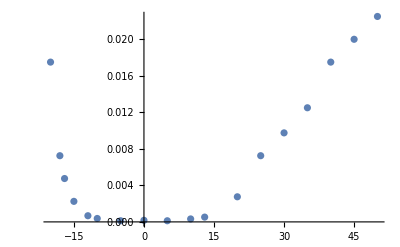

```mathematica
ListPlot[points,Joined->False]
```

```mathematica
ftrans=Interpolation[points]
```

InterpolatingFunction[…]

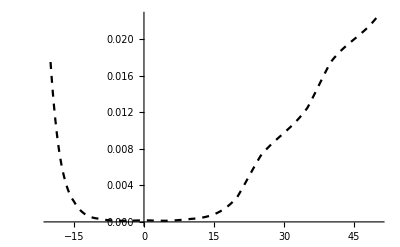

```mathematica
Plot[ftrans[x],{x,-20.,49.98738354037264},PlotStyle->{Black,Dashing[Small]}]
```

InterpolatingFunction::dmval: Input value {-21.9989} lies outside the range of data in the interpolating function. Extrapolation will be used.

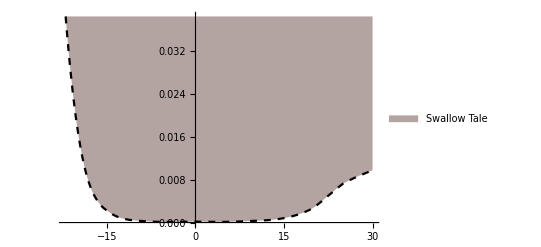

InterpolatingFunction::dmval: Input value {-21.9989} lies outside the range of data in the interpolating function. Extrapolation will be used.

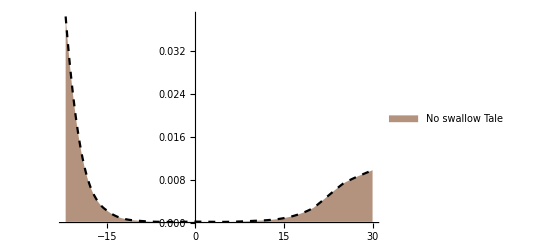

```mathematica
top=Plot[ftrans[x],{x,-22.,30},PlotStyle->{Black,Dashing[Small]},Filling->Top,FillingStyle->Hue[0.02,0.1,0.7],PlotLegends->SwatchLegend[{Hue[0.02,0.1,0.7]},{"Swallow Tale"}],PlotRange->All]
bottom=Plot[ftrans[x],{x,-22.,30},PlotStyle->{Black,Dashing[Small]},Filling->Bottom,FillingStyle->Hue[0.07,0.3,0.7],PlotLegends->SwatchLegend[{Hue[0.07,0.3,0.7]},{"No swallow Tale"}],PlotRange->All]
```

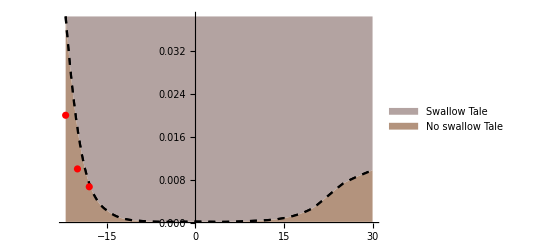

```mathematica
Show[top,bottom,ListPlot[data4,PlotStyle->Red]]
```

```mathematica
Export["phase.png",%]
```

phase.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["phase.png"]]]
```

```mathematica
data3={{-30,1/50,1.5909023597020697},{-30,1/100,1.592926650291994},{-30,1/150,1.593214253964642},{-30,1/200,1.5932952169939423},{-22,1/50,-1.2183570470846243},{-22,1/100,0.8252888794692681},{-22,1/150,1.226642591657801},{-22,1/200,1.400350608129853},{-21,1/50,-2.550411592007985},{-21,1/100,0.16781668993085747},{-21,1/150,0.9385944807056896},{-21,1/200,1.2287538204160773},{-20,1/50,-3.7529968343322},{-20,1/100,-0.5473629053794035},{-20,1/150,0.46733503118389963},{-20,1/200,0.9051598015584872},{-19,1/50,-4.736438327689074},{-19,1/100,-1.151610152284041},{-19,1/150,0.015074841307691985},{-19,1/200,1.226642591657801},{-18,1/50,-5.537313144326674},{-18,1/100,-1.684855843940438},{-18,1/150,-0.4037028124727754},{-18,1/200,0.9385944807056896},{-10,1/50,-11.854172232489965},{-10,1/100,-5.150392305183134},{-10,1/150,-2.8290385307424892}};
```

```mathematica
data4={{-22,1/50},{-20,1/100},{-18,1/150}}
```

{{-22,1/50},{-20,1/100},{-18,1/150}}

```mathematica
GeneralizedLinearModelFit[data4,{x},{x}]
```

FittedModel[-0.0544444-0.00333333 x]

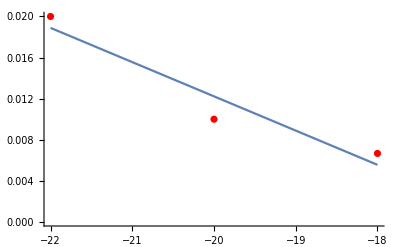

```mathematica
Show[ListPlot[data4,PlotStyle->Red],Plot[%158[x],{x,-22,-18}]]
```